```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M0-g,v[0]==0},v[t],t]
v1[t_]=v[t]/.sol1[[1]]
```

{{v[t]→(-g M0 t+A1 P1 t)/M0}}

(-g M0 t+A1 P1 t)/M0

```mathematica
M[t_]=M0-A1*ve*1000*t
sol2=DSolve[{v'[t]==-(ve/M[t])*M1'[t]-g,v[0]==vi1},v[t],t]
v2[t_]=v[t]/.sol2[[1]]
```

M0-1000 A1 t ve

{{v[t]→-g t+vi1}}

-g t+vi1

```mathematica
sol3=DSolve[{v'[t]==-g-(k*c*(v[t])^(2))/(M2),v[0]==vi2},v[t],t]
v3[t_]=v[t]/.sol3[[1]]
```

{{v[t]→(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k vi2)/(√g √M2)])/(√M2)])/(√c √k)}}

(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k vi2)/(√g √M2)])/(√M2)])/(√c √k)

```mathematica
sol4=DSolve[{v'[t]==-g+(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
v4[t_]=v[t]/.sol4[[1]]
```

{{v[t]→-(√g √M2 Tanh[(√c √g √k t)/(√M2)])/(√c √k)}}

-(√g √M2 Tanh[(√c √g √k t)/(√M2)])/(√c √k)

```mathematica
h1[t_]=Integrate[v1[t],t]

h2[t_]=Integrate[v2[t],t]

h3[t_]=Integrate[v3[t],t]

h4[t_]=Integrate[v4[t],t]+h1[t1]+h2[t2+t1]+h3[t3+t1+t2]
```

17.7312 t^2

3.95012 t-4.905 t^2

```mathematica
a1[t_]=D[v1[t],t]

a2[t_]=D[v2[t],t]

a3[t_]=D[v3[t],t]

a4[t_]=D[v4[t],t]
```

(-g M0+A1 P1)/M0

-g

-g Sec[(-√c √g √k t+√M2 ArcTan[(√c √k vi2)/(√g √M2)])/(√M2)]^2

-g Sech[(√c √g √k t)/(√M2)]^2

```mathematica
tsol1=Solve[h1[t]==L,t]
vi1=Simplify[v1[t]/.tsol1[[2]]]
```

{{t→-(√2 √L)/(√(-g+(A1 P1)/M0))},{t→(√2 √L)/(√(-g+(A1 P1)/M0))}}

√2 √L √(-g+(A1 P1)/M0)

```mathematica
tsol2=Solve[M[t]==0,t]
vi2=Simplify[v2[t]/.tsol2[[1]]]
```

{{t→M0/(1000 A1 ve)}}

√2 √L √(-g+(A1 P1)/M0)-(g M0)/(1000 A1 ve)

```mathematica
tsol3=Solve[v3[t]==0,t]

tsol4=Solve[h4[t]==0,t]
```

{{t→(√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M0)/(1000 A1 ve)))/(√g √M2)])/(√c √g √k)}}

{{t→ConditionalExpression[(2 ⅈ √M2 π C[1])/(√c √g √k),C[1]∈ℤ]}}

```mathematica
L=.22
A1=((4.75*10^(-3))^2)*Pi
A2=((.06)^2)*Pi
P1=4.4*10^5
P2=10^5
M0=0.6889
M2=.1889
g=9.81
ve=26.07680962
ρ1=1000
ρ2=1.22
c=0.1
k=ρ2*A2/2
```

0.22

0.0000708822

0.0113097

440000.

100000

0.6889

0.1889

9.81

26.0768

1000

1.22

0.1

0.00689894

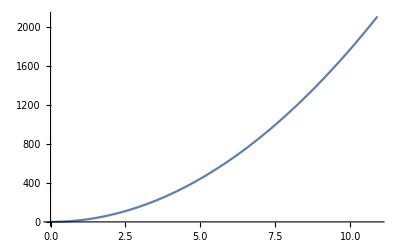

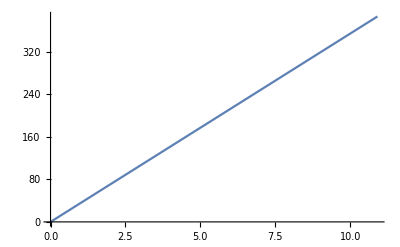

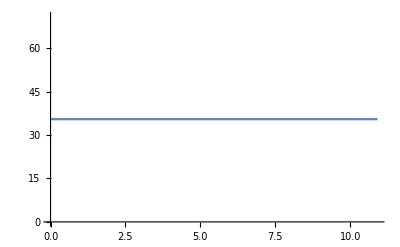

```mathematica
Plot[h1[t],{t,0,10.91}]

Plot[v1[t],{t,0,10.91}]

Plot[a1[t],{t,0,10.91}]
```

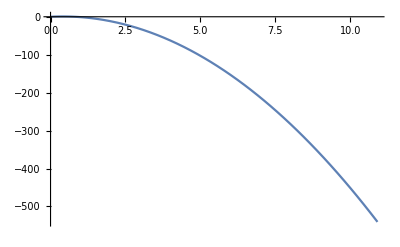

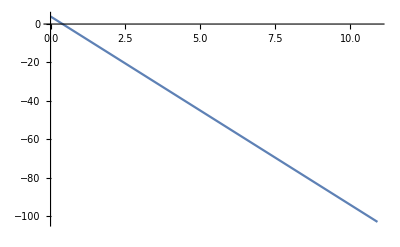

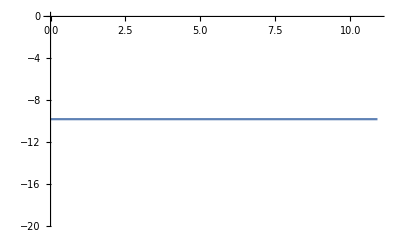

```mathematica
Plot[h2[t],{t,0,10.91}]

Plot[v2[t],{t,0,10.91}]

Plot[a2[t],{t,0,10.91}]
```

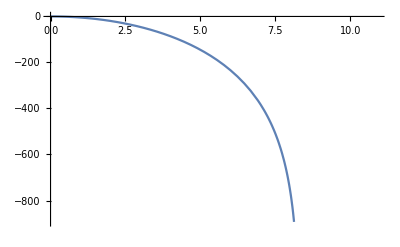

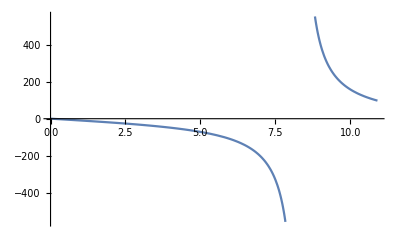

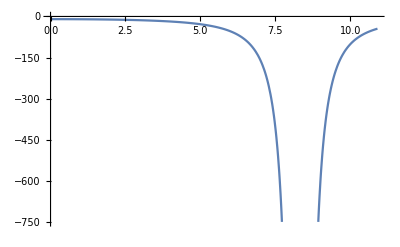

```mathematica
Plot[h3[t],{t,0,10.91}]

Plot[v3[t],{t,0,10.91}]

Plot[a3[t],{t,0,10.91}]
```

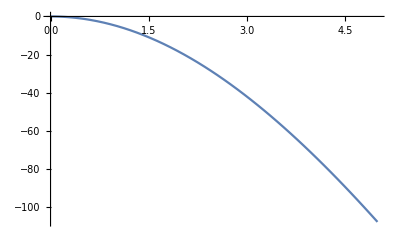

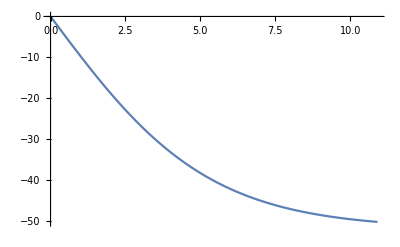

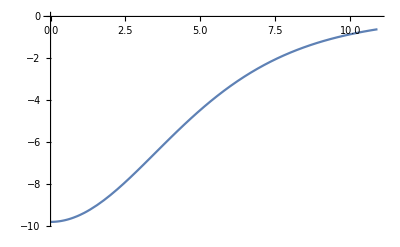

```mathematica
Plot[h4[t]-h4[0],{t,0,5}]

Plot[v4[t],{t,0,10.91}]

Plot[a4[t],{t,0,10.91}]
```

```mathematica
hcom[t_]:=h1[t]/;t<t1
hcom[t_]:=h2[t]/;t1<t<t2
hcom[t_]:=h3[t]/;t2<t<t3
hcom[t_]:=h4[t]/;t3<t<t4
```

```mathematica
Plot[hcom[t],{t,0,10}]
```

-Graphics-

```mathematica
t1=tsol1[[2]]
t2=tsol2[[1]]
t3=tsol3[[1]]
t4=tsol4[[1]]
```

{t→0.111389}

{t→0.372705}

{t→0.0299579}

{t→ConditionalExpression[(0.+33.1948 ⅈ) C[1],C[1]∈ℤ]}

```mathematica
hcom[t_]:=h1[t]/;t<t1
hcom[t_]:=h2[t]/;t1<t<t2
hcom[t_]:=h3[t]/;t2<t<t3
hcom[t_]:=h4[t]/;t3<t<t4
```

```mathematica
Plot[hcom[t],{t,0,10}]
```

-Graphics-

```mathematica
tsol4=Solve[h4[t]==0,t]
```

{{t→0.}}

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M0-g,v[0]==0},v[t],t]
v1[t_]=v[t]/.sol1[[1]]

M[t_]=M0-A1*ve*1000*t
sol2=DSolve[{v'[t]==-(ve/M[t])*M'[t]-g,v[0]==vi1},v[t],t]
v2[t_]=v[t]/.sol2[[1]]

sol3=DSolve[{v'[t]==-g-(k*c*(v[t])^(2))/(M2),v[0]==vi2},v[t],t]
v3[t_]=v[t]/.sol3[[1]]

sol4=DSolve[{v'[t]==-g+(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
v4[t_]=v[t]/.sol4[[1]]
```

{{v[t]→(-g M0 t+A1 P1 t)/M0}}

(-g M0 t+A1 P1 t)/M0

M0-1000 A1 t ve

{{v[t]→-g t+vi1+ve Log[M0]-ve Log[M0-1000 A1 t ve]}}

-g t+vi1+ve Log[M0]-ve Log[M0-1000 A1 t ve]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k vi2)/(√g √M2)])/(√M2)])/(√c √k)}}

(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k vi2)/(√g √M2)])/(√M2)])/(√c √k)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→-(√g √M2 Tanh[(√c √g √k t)/(√M2)])/(√c √k)}}

-(√g √M2 Tanh[(√c √g √k t)/(√M2)])/(√c √k)

```mathematica
h1[t_]=Integrate[v1[t],t]

h2[t_]=Integrate[v2[t],t]

h3[t_]=Integrate[v3[t],t]

h4[t_]=Integrate[v4[t],t]+h1[t1]+h2[t2+t1]+h3[t3+t1+t2]
```

17.7312 t^2

4.28992 t-4.905 t^2+9.71894 Log[0.372705-1. t]-26.0768 t Log[0.372705-1. t]

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

∫(v[t]/.{}⟦1⟧)ⅆt

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Integrate::ilim: Invalid integration variable or limit(s) in {(t→0.111389)+(t→0.372705)+(t→v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]])}.

{51.8274 t+Integrate[v[{(t→0.111389)+(t→0.372705)+(t→v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]])}]/.{}⟦1⟧,{(t→0.111389)+(t→0.372705)+(t→v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]])}]-273.81 Log[1.+ⅇ^(0.378564 t)]+9.71894 Log[0.372705-1. ((t→0.111389)+(t→0.372705))]+17.7312 (t→0.111389)^2+4.28992 ((t→0.111389)+(t→0.372705))-26.0768 Log[0.372705-1. ((t→0.111389)+(t→0.372705))] ((t→0.111389)+(t→0.372705))-4.905 ((t→0.111389)+(t→0.372705))^2}

```mathematica
a1[t_]=D[v1[t],t]

a2[t_]=D[v2[t],t]

a3[t_]=D[v3[t],t]

a4[t_]=D[v4[t],t]
```

(-g M0+A1 P1)/M0

-g+(1000 A1 ve^2)/(M0-1000 A1 t ve)

-g Sec[(-√c √g √k t+√M2 ArcTan[(√c √k vi2)/(√g √M2)])/(√M2)]^2

-g Sech[(√c √g √k t)/(√M2)]^2

```mathematica
tsol1=Solve[h1[t]==L,t]
vi1=Simplify[v1[t]/.tsol1[[2]]]

M[t_]=M0-A1*ve*1000*t
tsol2=Solve[M[t]==0,t]
vi2=Simplify[v2[t]/.tsol2[[1]]]

tsol3=Solve[v3[t]==0,t]

tsol4=Solve[h4[t]==0,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→h1^(-1)[L]}}

Part::partw: Part 2 of {{t→h1^(-1)[L]}} does not exist.

ReplaceAll::reps: {{{t→h1^(-1)[L]}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-g t+(A1 P1 t)/M0/.{{t→h1^(-1)[L]}}⟦2⟧

M0-1000 A1 t ve

{{t→M0/(1000 A1 ve)}}

Part::partw: Part 2 of {{M0/(1000 A1 ve)→h1^(-1)[L]}} does not exist.

ReplaceAll::reps: {{{M0/(1000 A1 ve)→h1^(-1)[L]}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-(g M0)/(1000 A1 ve)+ve ∞+ve Log[M0]+((-g M0+A1 P1)/(1000 A1 ve)/.{{M0/(1000 A1 ve)→h1^(-1)[L]}}⟦2⟧)

Solve::infc: The system (√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[Times[«5»]])/(√M2)])/(√c √k)==0 contains an infinite object ∞.

Solve[(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k (-(g M0)/(1000 A1 ve)+ve ∞+ve Log[M0]+((-g M0+A1 P1)/(1000 A1 ve)/.{{M0/(1000 A1 ve)→h1^(-1)[L]}}⟦2⟧)))/(√g √M2)])/(√M2)])/(√c √k)==0,t]

Solve::infc: The system -1/2 g (t1+t2)^2+(t1+t2) ve+h1[t1]+(t1+t2) ve Log[M0]+(M0 Log[M0-1000 A1 (t1+t2) ve])/(1000 A1)-(t1+t2) ve Log[M0-1000 A1 (t1+t2) ve]+(M2 Log[Cos[Power[«2»] Power[«2»] Power[«2»] Power[«2»] Plus[«3»]-ArcTan[«1»]]])/(c k)-(M2 Log[Cosh[(√c √g √k t)/(√M2)]])/(c k)+(t1+t2) (-g t+(A1 P1 t)/M0/.{{Rule[«2»]}}⟦2⟧)==0 contains an infinite object ∞.

Solve[-1/2 g (t1+t2)^2+(t1+t2) ve+h1[t1]+(t1+t2) ve Log[M0]+(M0 Log[M0-1000 A1 (t1+t2) ve])/(1000 A1)-(t1+t2) ve Log[M0-1000 A1 (t1+t2) ve]+1/(c k)M2 Log[Cos[(√c √g √k (t1+t2+t3))/(√M2)-ArcTan[(√c √k (-(g M0)/(1000 A1 ve)+ve ∞+ve Log[M0]+((-g M0+A1 P1)/(1000 A1 ve)/.{{M0/(1000 A1 ve)→h1^(-1)[L]}}⟦2⟧)))/(√g √M2)]]]-(M2 Log[Cosh[(√c √g √k t)/(√M2)]])/(c k)+(t1+t2) (-g t+(A1 P1 t)/M0/.{{t→h1^(-1)[L]}}⟦2⟧)==0,t]

```mathematica
t1=tsol1[[2]]
t2=tsol2[[1]]
t3=tsol3[[1]]
t4=tsol4[[1]]
```

Part::partw: Part 2 of {{t→h1^(-1)[0.22]}} does not exist.

{{t→h1^(-1)[0.22]}}⟦2⟧

{t→0.372705}

Part::partw: Part 2 of {{0.372705→h1^(-1)[0.22]}} does not exist.

ReplaceAll::reps: {{{0.372705→h1^(-1)[0.22]}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{t→8.2987}

Part::partw: Part 2 of {{0.372705→h1^(-1)[0.22]}} does not exist.

ReplaceAll::reps: {{{0.372705→h1^(-1)[0.22]}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {{t→h1^(-1)[0.22]}} does not exist.

ReplaceAll::reps: {{{t→h1^(-1)[0.22]}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {{System`TSolveDump`X$18847[1]→h1^(-1)[0.22]}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{{System`TSolveDump`X$18847[1]→h1^(-1)[0.22]}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

{h1[{{t→h1^(-1)[0.22]}}⟦2⟧]-273.81 Log[Cosh[0.189282 t]]+9.71894 Log[0.6889-1.84838 ({{t→h1^(-1)[0.22]}}⟦2⟧+(t→0.372705))]+273.81 Log[Sin[0.189282 ({{t→h1^(-1)[0.22]}}⟦2⟧+(t→0.372705)+(t→8.2987))]]+16.359 ({{t→h1^(-1)[0.22]}}⟦2⟧+(t→0.372705))-26.0768 Log[0.6889-1.84838 ({{t→h1^(-1)[0.22]}}⟦2⟧+(t→0.372705))] ({{t→h1^(-1)[0.22]}}⟦2⟧+(t→0.372705))+(35.4624 t/.{{t→h1^(-1)[0.22]}}⟦2⟧) ({{t→h1^(-1)[0.22]}}⟦2⟧+(t→0.372705))-4.905 ({{t→h1^(-1)[0.22]}}⟦2⟧+(t→0.372705))^2}==0

```mathematica
L=.22
A1=((4.75*10^(-3))^2)*Pi
A2=((.06)^2)*Pi
P1=4.4*10^5
P2=10^5
M0=0.6889
M2=.1889
g=9.81
ve=26.07680962
ρ1=1000
ρ2=1.22
c=0.1
k=ρ2*A2/2
```

0.22

0.0000708822

0.0113097

440000.

100000

0.6889

0.1889

9.81

26.0768

1000

1.22

0.1

0.00689894

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M0-g,v[0]==0},v[t],t]
v1[t_]=v[t]/.sol1[[1]]

M[t_]=M0-A1*ve*1000*t
sol2=DSolve[{v'[t]==-(ve/M[t])*M'[t]-g,v[0]==vi1},v[t],t]
v2[t_]=v[t]/.sol2[[1]]

sol3=DSolve[{v'[t]==-g-(k*c*(v[t])^(2))/(M2),v[0]==vi2},v[t],t]
v3[t_]=v[t]/.sol3[[1]]

sol4=DSolve[{v'[t]==-g+(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
v4[t_]=v[t]/.sol4[[1]]


h1[t_]=Integrate[v1[t],t]

h2[t_]=Integrate[v2[t],t]

h3[t_]=Integrate[v3[t],t]

h4[t_]=Integrate[v4[t],t]+120


a1[t_]=D[v1[t],t]

a2[t_]=D[v2[t],t]

a3[t_]=D[v3[t],t]

a4[t_]=D[v4[t],t]


tsol1=Solve[h1[t]==L,t]
vi1=Simplify[v1[t]/.tsol1[[2]]]

M[t_]=M0-A1*ve*1000*t
tsol2=Solve[M[t]==0,t]
vi2=Simplify[v2[t]/.tsol2[[1]]]

tsol3=Solve[v3[t]==0,t]

tsol4=Solve[h4[t]==0,t]

t1=tsol1[[2]]
t2=tsol2[[1]]
t3=tsol3[[1]]
t4=tsol4[[1]]
```

{{v[t]→35.4624 t}}

35.4624 t

0.6889-1.84838 t

{{v[t]→-21.7869-9.81 t-26.0768 Log[0.372705-1. t]}}

-21.7869-9.81 t-26.0768 Log[0.372705-1. t]

{}

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

v[t]/.{}⟦1⟧

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→-(51.8274 (-1.+1. ⅇ^(0.378564 t)))/(1.+1. ⅇ^(0.378564 t))}}

-(51.8274 (-1.+1. ⅇ^(0.378564 t)))/(1.+1. ⅇ^(0.378564 t))

17.7312 t^2

4.28992 t-4.905 t^2+9.71894 Log[0.372705-1. t]-26.0768 t Log[0.372705-1. t]

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

∫(v[t]/.{}⟦1⟧)ⅆt

120+51.8274 t-273.81 Log[1.+ⅇ^(0.378564 t)]

35.4624

-9.81+26.0768/(0.372705-1. t)

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

∂_t (v[t]/.{}⟦1⟧)

(19.62 ⅇ^(0.378564 t) (-1.+1. ⅇ^(0.378564 t)))/((1.+1. ⅇ^(0.378564 t))^2)-(19.62 ⅇ^(0.378564 t))/(1.+1. ⅇ^(0.378564 t))

{{t→-0.111389},{t→0.111389}}

3.95012

0.6889-1.84838 t

{{t→0.372705}}

Indeterminate

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]]}}

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[120+51.8274 t-273.81 Log[1.+ⅇ^(0.378564 t)]==0,t]

{t→0.111389}

{t→0.372705}

{t→v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]]}

120+51.8274 t-273.81 Log[1.+ⅇ^(0.378564 t)]==0

```mathematica
L=.22
A1=((4.75*10^(-3))^2)*Pi
A2=((.06)^2)*Pi
P1=4.4*10^5
P2=10^5
M0=0.6889
M2=.1889
g=9.81
ve=26.07680962
ρ1=1000
ρ2=1.22
c=0.1
k=ρ2*A2/2
```

0.22

0.0000708822

0.0113097

440000.

100000

0.6889

0.1889

9.81

26.0768

1000

1.22

0.1

0.00689894

```mathematica
hcom[t_]:=h1[t]/;t<t1
hcom[t_]:=h2[t]/;t1<t<t2
hcom[t_]:=h3[t]/;t2<t<t3
hcom[t_]:=h4[t]/;t3<t<t4
```

```mathematica
Plot[hcom[t],{t,0,10}]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

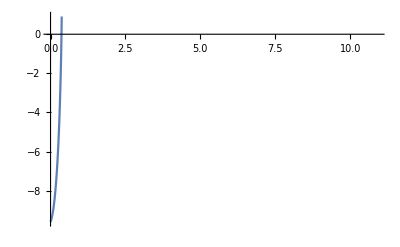

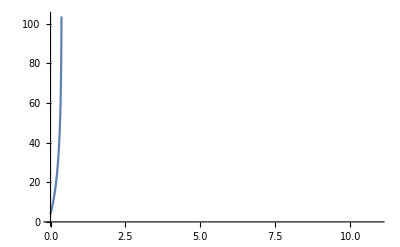

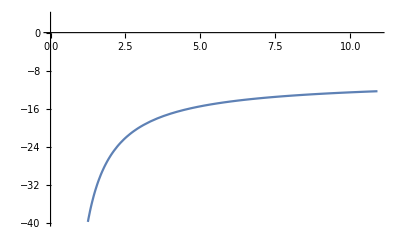

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Integrate::ilim: Invalid integration variable or limit(s) in 0.000222876.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Integrate::ilim: Invalid integration variable or limit(s) in 0.222876.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Integrate::ilim: Invalid integration variable or limit(s) in 0.445529.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

-Graphics-

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 0.000222876 is not a valid variable.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 0.222876 is not a valid variable.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

General::ivar: 0.445529 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Integrate::ilim: Invalid integration variable or limit(s) in {(0.000102143→0.111389)+(0.000102143→0.372705)+(0.000102143→v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]])}.

NIntegrate::ilim: Invalid integration variable or limit(s) in {(0.000102143→0.111389)+(0.000102143→0.372705)+(0.000102143→v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]])}.

NIntegrate::ilim: Invalid integration variable or limit(s) in {(0.000102143→0.111389)+(0.000102143→0.372705)+(0.000102143→v^(-1)[InverseFunction[ReplaceAll,1,2][0.,{}⟦1⟧]])}.

General::stop: Further output of NIntegrate::ilim will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Integrate::ilim: Invalid integration variable or limit(s) in {(0.102143→0.111389)+(0.102143→0.372705)+(0.102143→v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]])}.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Integrate::ilim: Invalid integration variable or limit(s) in {(0.204184→0.111389)+(0.204184→0.372705)+(0.204184→v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]])}.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

-Graphics-

-Graphics-

-Graphics-

```mathematica
Plot[h1[t],{t,0,10.91}]

Plot[v1[t],{t,0,10.91}]

Plot[a1[t],{t,0,10.91}]


Plot[h2[t],{t,0,10.91}]

Plot[v2[t],{t,0,10.91}]

Plot[a2[t],{t,0,10.91}]


Plot[h3[t],{t,0,10.91}]

Plot[v3[t],{t,0,10.91}]

Plot[a3[t],{t,0,10.91}]


Plot[h4[t],{t,0,5}]

Plot[v4[t],{t,0,10.91}]

Plot[a4[t],{t,0,10.91}]
```

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M0-g,v[0]==0},v[t],t]
v1[t_]=v[t]/.sol1[[1]]

M[t_]=M0-A1*ve*1000*t
sol2=DSolve[{v'[t]==-(ve/M[t])*M'[t]-g,v[0]==vi1},v[t],t]
v2[t_]=v[t]/.sol2[[1]]

sol3=DSolve[{v'[t]==-g-(k*c*(v[t])^(2))/(M2),v[0]==vi2},v[t],t]
v3[t_]=v[t]/.sol3[[1]]

sol4=DSolve[{v'[t]==-g+(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
v4[t_]=v[t]/.sol4[[1]]


h1[t_]=Integrate[v1[t],t]

h2[t_]=Integrate[v2[t],t]

h3[t_]=Integrate[v3[t],t]

h4[t_]=Integrate[v4[t],t]

h4[0]=h1[t1]+h2[t2+t1]+h3[t3+t1+t2]


a1[t_]=D[v1[t],t]

a2[t_]=D[v2[t],t]

a3[t_]=D[v3[t],t]

a4[t_]=D[v4[t],t]


tsol1=Solve[h1[t]==L,t]
vi1=Simplify[v1[t]/.tsol1[[2]]]

M[t_]=M0-A1*ve*1000*t
tsol2=Solve[M[t]==0,t]
vi2=Simplify[v2[t]/.tsol2[[1]]]

tsol3=Solve[v3[t]==0,t]

tsol4=Solve[h4[t]==0,t]

t1=tsol1[[2]]
t2=tsol2[[1]]
t3=tsol3[[1]]
t4=tsol4[[1]]
```

{{v[t]→35.4624 t}}

35.4624 t

0.6889-1.84838 t

{{v[t]→-21.7869-9.81 t-26.0768 Log[0.372705-1. t]}}

-21.7869-9.81 t-26.0768 Log[0.372705-1. t]

{}

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

v[t]/.{}⟦1⟧

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→-(51.8274 (-1.+1. ⅇ^(0.378564 t)))/(1.+1. ⅇ^(0.378564 t))}}

-(51.8274 (-1.+1. ⅇ^(0.378564 t)))/(1.+1. ⅇ^(0.378564 t))

17.7312 t^2

4.28992 t-4.905 t^2+9.71894 Log[0.372705-1. t]-26.0768 t Log[0.372705-1. t]

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

∫(v[t]/.{}⟦1⟧)ⅆt

51.8274 t-273.81 Log[1.+ⅇ^(0.378564 t)]

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Integrate::ilim: Invalid integration variable or limit(s) in t1+t2+t3.

17.7312 t1^2+4.28992 (t1+t2)-4.905 (t1+t2)^2+∫(v[t1+t2+t3]/.{}⟦1⟧)ⅆ(t1+t2+t3)+9.71894 Log[0.372705-1. (t1+t2)]-26.0768 (t1+t2) Log[0.372705-1. (t1+t2)]

35.4624

-9.81+26.0768/(0.372705-1. t)

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

∂_t (v[t]/.{}⟦1⟧)

(19.62 ⅇ^(0.378564 t) (-1.+1. ⅇ^(0.378564 t)))/((1.+1. ⅇ^(0.378564 t))^2)-(19.62 ⅇ^(0.378564 t))/(1.+1. ⅇ^(0.378564 t))

{{t→-0.111389},{t→0.111389}}

3.95012

0.6889-1.84838 t

{{t→0.372705}}

Indeterminate

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]]}}

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[51.8274 t-273.81 Log[1.+ⅇ^(0.378564 t)]==0,t]

{t→0.111389}

{t→0.372705}

{t→v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]]}

51.8274 t-273.81 Log[1.+ⅇ^(0.378564 t)]==0

```mathematica
L=.22
A1=((4.75*10^(-3))^2)*Pi
A2=((.06)^2)*Pi
P1=4.4*10^5
P2=10^5
M0=0.6889
M2=.1889
g=9.81
ve=26.07680962
ρ1=1000
ρ2=1.22
c=0.1
k=ρ2*A2/2
```

0.22

0.0000708822

0.0113097

440000.

100000

0.6889

0.1889

9.81

26.0768

1000

1.22

0.1

0.00689894

```mathematica
Plot[h4[t]-h4[0],{t,0,5}]

Plot[v4[t],{t,0,10.91}]

Plot[a4[t],{t,0,10.91}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
h4[0]
```

{9.71894 Log[0.6889-1.84838 ((t→0.111389)+(t→0.372705))]+273.81 Log[Sin[0.189282 ((51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0)+(t→0.111389)+(t→0.372705))]]+17.7312 (t→0.111389)^2+20.3092 ((t→0.111389)+(t→0.372705))-26.0768 Log[0.6889-1.84838 ((t→0.111389)+(t→0.372705))] ((t→0.111389)+(t→0.372705))-4.905 ((t→0.111389)+(t→0.372705))^2}

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M0-g,v[0]==0},v[t],t]
v1[t_]=v[t]/.sol1[[1]]

M[t_]=M0-A1*ve*1000*t
sol2=DSolve[{v'[t]==-(ve/M[t])*M'[t]-g,v[0]==vi1},v[t],t]
v2[t_]=v[t]/.sol2[[1]]

sol3=DSolve[{v'[t]==-g-(k*c*(v[t])^(2))/(M2),v[0]==vi2},v[t],t]
v3[t_]=v[t]/.sol3[[1]]

sol4=DSolve[{v'[t]==-g+(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
v4[t_]=v[t]/.sol4[[1]]


h1[t_]=Integrate[v1[t],t]

h2[t_]=Integrate[v2[t],t]

h3[t_]=Integrate[v3[t],t]

h4[t_]=Integrate[v4[t],t]




a1[t_]=D[v1[t],t]

a2[t_]=D[v2[t],t]

a3[t_]=D[v3[t],t]

a4[t_]=D[v4[t],t]


tsol1=Solve[h1[t1]==L,t1]
vi1=Simplify[v1[t1]/.tsol1[[2]]]

M[t_]=M0-A1*ve*1000*t
tsol2=Solve[M[t2]==0,t2]
vi2=Simplify[v2[t2]/.tsol2[[1]]]

tsol3=Solve[v3[t3]==0,t3]

tsol4=Solve[h4[t4]==0,t4]
```

{{v[t]→35.4624 t}}

35.4624 t

0.6889-1.84838 t

{{v[t]→-21.7869-9.81 t-26.0768 Log[0.372705-1. t]}}

-21.7869-9.81 t-26.0768 Log[0.372705-1. t]

{}

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

v[t]/.{}⟦1⟧

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→-(51.8274 (-1.+1. ⅇ^(0.378564 t)))/(1.+1. ⅇ^(0.378564 t))}}

-(51.8274 (-1.+1. ⅇ^(0.378564 t)))/(1.+1. ⅇ^(0.378564 t))

17.7312 t^2

4.28992 t-4.905 t^2+9.71894 Log[0.372705-1. t]-26.0768 t Log[0.372705-1. t]

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

∫(v[t]/.{}⟦1⟧)ⅆt

51.8274 t-273.81 Log[1.+ⅇ^(0.378564 t)]

35.4624

-9.81+26.0768/(0.372705-1. t)

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

∂_t (v[t]/.{}⟦1⟧)

(19.62 ⅇ^(0.378564 t) (-1.+1. ⅇ^(0.378564 t)))/((1.+1. ⅇ^(0.378564 t))^2)-(19.62 ⅇ^(0.378564 t))/(1.+1. ⅇ^(0.378564 t))

{{t1→-0.111389},{t1→0.111389}}

3.95012

0.6889-1.84838 t

{{t2→0.372705}}

Indeterminate

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t3→v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]]}}

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[51.8274 t4-273.81 Log[1.+ⅇ^(0.378564 t4)]==0,t4]

```mathematica
L=.22
A1=((4.75*10^(-3))^2)*Pi
A2=((.06)^2)*Pi
P1=4.4*10^5
P2=10^5
M0=0.6889
M2=.1889
g=9.81
ve=26.07680962
ρ1=1000
ρ2=1.22
c=0.1
k=ρ2*A2/2

hcom[t_]:=h1[t]/;t<t1
hcom[t_]:=h2[t]/;t1<t<t2
hcom[t_]:=h3[t]/;t2<t<t3
hcom[t_]:=h4[t]/;t3<t<t4
```

0.22

0.0000708822

0.0113097

440000.

100000

0.6889

0.1889

9.81

26.0768

1000

1.22

0.1

0.00689894

```mathematica
Clear[h4]
```

```mathematica
Plot[h3[t],{t,0,10.91}]

Plot[v3[t],{t,0,10.91}]

Plot[a3[t],{t,0,10.91}]


Plot[h4[t]-h4[0],{t,0,5}]

Plot[v4[t],{t,0,10.91}]

Plot[a4[t],{t,0,10.91}]
```

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Integrate::ilim: Invalid integration variable or limit(s) in 0.000222876.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Integrate::ilim: Invalid integration variable or limit(s) in 0.222876.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Integrate::ilim: Invalid integration variable or limit(s) in 0.445529.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

-Graphics-

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 0.000222876 is not a valid variable.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 0.222876 is not a valid variable.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

General::ivar: 0.445529 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
t3
```

{t→v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]]}

```mathematica
t2
```

{t→0.372705}

{{v[t]→35.4624 t}}

35.4624 t

0.6889-1.84838 t

{{v[t]→-21.7869-9.81 t-26.0768 Log[0.372705-1. t]}}

-21.7869-9.81 t-26.0768 Log[0.372705-1. t]

{}

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

v[t]/.{}⟦1⟧

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→-(51.8274 (-1.+1. ⅇ^(0.378564 t)))/(1.+1. ⅇ^(0.378564 t))}}

-(51.8274 (-1.+1. ⅇ^(0.378564 t)))/(1.+1. ⅇ^(0.378564 t))

17.7312 t^2

4.28992 t-4.905 t^2+9.71894 Log[0.372705-1. t]-26.0768 t Log[0.372705-1. t]

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

∫(v[t]/.{}⟦1⟧)ⅆt

51.8274 t-273.81 Log[1.+ⅇ^(0.378564 t)]

35.4624

-9.81+26.0768/(0.372705-1. t)

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

∂_t (v[t]/.{}⟦1⟧)

(19.62 ⅇ^(0.378564 t) (-1.+1. ⅇ^(0.378564 t)))/((1.+1. ⅇ^(0.378564 t))^2)-(19.62 ⅇ^(0.378564 t))/(1.+1. ⅇ^(0.378564 t))

{{t→-0.111389},{t→0.111389}}

3.95012

0.6889-1.84838 t

{{t→0.372705}}

Indeterminate

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]]}}

ReplaceAll::reps: {51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Integrate::ilim: Invalid integration variable or limit(s) in 0.484093+(t/.51.8274 Tan[2.30083 (0.682709+Times[«2»])]==0).

ReplaceAll::reps: {51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Integrate::ilim: Invalid integration variable or limit(s) in 0.484093+(System`TSolveDump`X$5470[1]/.51.8274 Tan[2.30083 (0.682709+Times[«2»])]==0).

Integrate::ilim: Invalid integration variable or limit(s) in 23800655/49165411+(System`TSolveDump`X$5470[1]/.(484721255 Tan[(75987449 (80060187/117268331+Times[«2»]))/33026142])/9352607==0).

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[∫(v[0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0)]/.{}⟦1⟧)ⅆ(0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0))-273.81 Log[Cosh[0.189282 t]]+273.81 Log[Sin[0.189282 (0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0))]]==0,t]

0.22

0.0000708822

0.0113097

440000.

100000

0.6889

0.1889

9.81

26.0768

1000

1.22

0.1

0.00689894

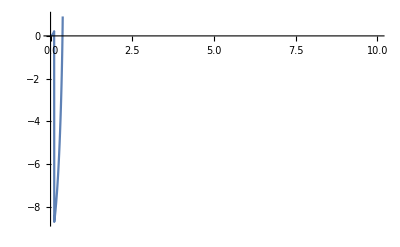

-Graphics-

-Graphics-

-Graphics-

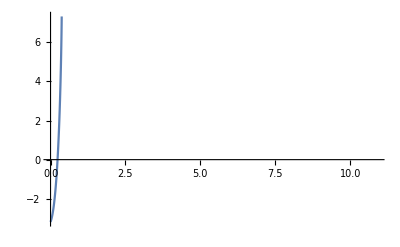

-Graphics-

-Graphics-

-Graphics-

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 0.000222876 is not a valid variable.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 0.222876 is not a valid variable.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

General::ivar: 0.445529 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

ReplaceAll::reps: {False} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {False} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Integrate::ilim: Invalid integration variable or limit(s) in 0.484093+(0.000102143/.False).

Integrate::ilim: Invalid integration variable or limit(s) in 0.484093+(0.102143/.False).

Integrate::ilim: Invalid integration variable or limit(s) in 0.484093+(0.204184/.False).

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

-Graphics-

-Graphics-

-Graphics-

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M0-g,v[0]==0},v[t],t]
v1[t_]=v[t]/.sol1[[1]]

M[t_]=M0-A1*ve*1000*t
sol2=DSolve[{v'[t]==-(ve/M[t])*M'[t]-g,v[0]==vi1},v[t],t]
v2[t_]=v[t]/.sol2[[1]]

sol3=DSolve[{v'[t]==-g-(k*c*(v[t])^(2))/(M2),v[0]==vi2},v[t],t]
v3[t_]=v[t]/.sol3[[1]]

sol4=DSolve[{v'[t]==-g+(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
v4[t_]=v[t]/.sol4[[1]]


h1[t_]=Integrate[v1[t],t]

h2[t_]=Integrate[v2[t],t]

h3[t_]=Integrate[v3[t],t]

h4[t_]=Integrate[v4[t],t]


a1[t_]=D[v1[t],t]

a2[t_]=D[v2[t],t]

a3[t_]=D[v3[t],t]

a4[t_]=D[v4[t],t]


tsol1=Solve[h1[t]==L,t]
vi1=Simplify[v1[t]/.tsol1[[2]]]

M[t_]=M0-A1*ve*1000*t
tsol2=Solve[M[t]==0,t]
vi2=Simplify[v2[t]/.tsol2[[1]]]

tsol3=Solve[v3[t]==0,t]

tsol4=Solve[h4[t]==0,t]


L=.22
A1=((4.75*10^(-3))^2)*Pi
A2=((.06)^2)*Pi
P1=4.4*10^5
P2=10^5
M0=0.6889
M2=.1889
g=9.81
ve=26.07680962
ρ1=1000
ρ2=1.22
c=0.1
k=ρ2*A2/2

hcom[t_]:=h1[t]/;t<t1
hcom[t_]:=h2[t]/;t1<t<t2
hcom[t_]:=h3[t]/;t2<t<t3
hcom[t_]:=h4[t]/;t3<t<t4

Plot[hcom[t],{t,0,10}]


Plot[h1[t],{t,0,10.91}]

Plot[v1[t],{t,0,10.91}]

Plot[a1[t],{t,0,10.91}]


Plot[h2[t],{t,0,10.91}]

Plot[v2[t],{t,0,10.91}]

Plot[a2[t],{t,0,10.91}]


Plot[h3[t],{t,0,10.91}]

Plot[v3[t],{t,0,10.91}]

Plot[a3[t],{t,0,10.91}]


Plot[h4[t]-h4[0],{t,0,5}]

Plot[v4[t],{t,0,10.91}]

Plot[a4[t],{t,0,10.91}]

h1com[t_]:=h1[t]/;t<t1
h2com[t_]:=h2sol[t]/;t1<t<t2
h3com[t_]:=h3sol[t]/;t2<t<t3
h4com[t_]:=h4sol[t]/;t3<t<t4
```

```mathematica
t1
```

t1

```mathematica
t1 = tsol1[[2]]
```

{t→0.111389}

```mathematica
t1
```

{t→0.111389}

```mathematica
t1
```

{t→0.111389}

```mathematica
Information[t1]
```

Global`t1

t1={t→0.111389}

```mathematica
t1 + 3
```

{3+(t→0.111389)}

```mathematica
t1
```

{t→0.111389}

```mathematica
t1/.tsol1[[2]]
```

{0.111389→0.111389}

```mathematica
t1
```

{t→0.111389}

```mathematica
t1 = tsol1[[2]]
```

{t→0.111389}

```mathematica
t1 = t
```

t

```mathematica
t1
```

t

```mathematica
t1 = tsol1[[2]]
```

{t→0.111389}

```mathematica
t/.t1
```

0.111389

```mathematica
t1
```

{t→0.111389}

```mathematica
x = t/.t1
```

0.111389

```mathematica
x
```

0.111389

```mathematica
t1=tsol1[[2]]
t1=t/.t1

t2=tsol2[[1]]
t2=t/.t2+t1

t3=tsol3[[1]]
t3=t/.t3+t2

t4=tsol1[[1]]
t4=t/.t4+t3
```

{t→0.111389}

0.111389

{t→0.372705}

ReplaceAll::reps: {0.111389+(t→0.372705)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

t/.{0.111389+(t→0.372705)}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{t→8.2987}

ReplaceAll::reps: {(t/.{0.111389+(t→0.372705)})+(t→8.2987)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

t/.{(t/.{0.111389+(t→0.372705)})+(t→8.2987)}

{t→-0.111389}

ReplaceAll::reps: {(t/.{(t/.{Plus[«2»]})+(t→8.2987)})+(t→-0.111389)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

t/.{(t/.{(t/.{0.111389+(t→0.372705)})+(t→8.2987)})+(t→-0.111389)}

```mathematica
t2=tsol2[[1]]
t2=t/.t2
t2=t2+t1
```

{t→0.372705}

0.372705

0.484093

```mathematica
t1=tsol1[[2]]
t1=t/.t1

t2=tsol2[[1]]
t2=t/.t2
t2=t2+t1

t3=tsol3[[1]]
t3=t/.t3
t3=t3+t2

t4=tsol4[[1]]
t4=t/.t4
t4=t4+t3
```

{t→0.111389}

0.111389

{t→0.372705}

0.372705

0.484093

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{t→8.2987}

8.2987

8.7828

{t→ConditionalExpression[(0.+33.1948 ⅈ) C[1],C[1]∈ℤ]}

ConditionalExpression[(0.+33.1948 ⅈ) C[1],C[1]∈ℤ]

ConditionalExpression[8.7828+(0.+33.1948 ⅈ) C[1],C[1]∈ℤ]

```mathematica
hcom[t_]:=h1[t]/;t<t1
hcom[t_]:=h2[t]/;t1<t<t2
hcom[t_]:=h3[t]/;t2<t<t3
hcom[t_]:=h4[t]/;t3<t<t4
```

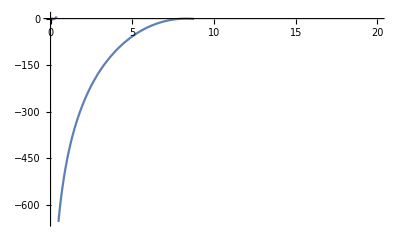

```mathematica
Plot[hcom[t],{t,0,20}]
```

```mathematica
h2[t_]=h2[t_]+h1[t1]
```

Rule::rhs: Pattern t_ appears on the right-hand side of rule h2[t_]→0.22+9.71894 Log[0.6889-1.84838 t_]+20.3092 t_-26.0768 Log[0.6889-1.84838 t_] t_-4.905 t_^2.

General::stop: Further output of Rule::rhs will be suppressed during this calculation.

0.22+9.71894 Log[0.6889-1.84838 t_]+20.3092 t_-26.0768 Log[0.6889-1.84838 t_] t_-4.905 t_^2

```mathematica
h2[t]=h2[t]+h1[t1]
```

0.66+9.71894 Log[0.6889-1.84838 t_]+20.3092 t_-26.0768 Log[0.6889-1.84838 t_] t_-4.905 t_^2

```mathematica
h1[t_]=Integrate[v1[t],t]

h2[t_]=Integrate[v2[t],t]
h2[t]=h2[t]+h1[t1]

h3[t_]=Integrate[v3[t],t]
h3[t]=h3[t]+h2[t2]

h4[t_]=Integrate[v4[t],t]
h4[t]=h4[t]+h3[t3]
```

17.7312 t^2

20.3092 t-4.905 t^2+9.71894 Log[0.6889-1.84838 t]-26.0768 t Log[0.6889-1.84838 t]

0.88+9.71894 Log[0.6889-1.84838 t_]+20.3092 t_-26.0768 Log[0.6889-1.84838 t_] t_-4.905 t_^2

```mathematica
hcom[t_]:=h1[t]/;t<t1
hcom[t_]:=h2[t]/;t1<t<t2
hcom[t_]:=h3[t]/;t2<t<t3
hcom[t_]:=h4[t]/;t3<t<t4

Plot[hcom[t],{t,0,10}]
```

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M0-g,v[0]==0},v[t],t]
v1[t_]=v[t]/.sol1[[1]]

M[t_]=M0-A1*ve*1000*t
sol2=DSolve[{v'[t]==-(ve/M[t])*M'[t]-g,v[0]==vi1},v[t],t]
v2[t_]=v[t]/.sol2[[1]]

sol3=DSolve[{v'[t]==-g-(k*c*(v[t])^(2))/(M2),v[0]==vi2},v[t],t]
v3[t_]=v[t]/.sol3[[1]]

sol4=DSolve[{v'[t]==-g+(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
v4[t_]=v[t]/.sol4[[1]]


h1[t_]=Integrate[v1[t],t]

h2[t_]=Integrate[v2[t],t]
h2[t]=h2[t]+h1[t1]

h3[t_]=Integrate[v3[t],t]
h3[t]=h3[t]+h2[t2]

h4[t_]=Integrate[v4[t],t]
h4[t]=h4[t]+h3[t3]

a1[t_]=D[v1[t],t]

a2[t_]=D[v2[t],t]

a3[t_]=D[v3[t],t]

a4[t_]=D[v4[t],t]


tsol1=Solve[h1[t]==L,t]
vi1=Simplify[v1[t]/.tsol1[[2]]]

M[t_]=M0-A1*ve*1000*t
tsol2=Solve[M[t]==0,t]
vi2=Simplify[v2[t]/.tsol2[[1]]]

tsol3=Solve[v3[t]==0,t]

tsol4=Solve[h4[t]==0,t]

t1=tsol1[[2]]
t1=t/.t1

t2=tsol2[[1]]
t2=t/.t2
t2=t2+t1

t3=tsol3[[1]]
t3=t/.t3
t3=t3+t2

t4=tsol4[[1]]
t4=t/.t4
t4=t4+t3
```

{{v[t]→35.4624 t}}

35.4624 t

0.6889-1.84838 t

{{v[t]→-21.7869-9.81 t-26.0768 Log[0.372705-1. t]}}

-21.7869-9.81 t-26.0768 Log[0.372705-1. t]

{}

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

v[t]/.{}⟦1⟧

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→-(51.8274 (-1.+1. ⅇ^(0.378564 t)))/(1.+1. ⅇ^(0.378564 t))}}

-(51.8274 (-1.+1. ⅇ^(0.378564 t)))/(1.+1. ⅇ^(0.378564 t))

17.7312 t^2

4.28992 t-4.905 t^2+9.71894 Log[0.372705-1. t]-26.0768 t Log[0.372705-1. t]

0.44+20.3092 t-4.905 t^2+9.71894 Log[0.6889-1.84838 t]-26.0768 t Log[0.6889-1.84838 t]

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

∫(v[t]/.{}⟦1⟧)ⅆt

(20.5749-18.2506 ⅈ)+273.81 Log[Sin[0.189282 t]]

51.8274 t-273.81 Log[1.+ⅇ^(0.378564 t)]

ReplaceAll::reps: {51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Integrate::ilim: Invalid integration variable or limit(s) in 0.484093+(t/.51.8274 Tan[2.30083 (0.682709+Times[«2»])]==0).

∫(v[0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0)]/.{}⟦1⟧)ⅆ(0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0))-273.81 Log[Cosh[0.189282 t]]+273.81 Log[Sin[0.189282 (0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0))]]

35.4624

-9.81+26.0768/(0.372705-1. t)

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

∂_t (v[t]/.{}⟦1⟧)

(19.62 ⅇ^(0.378564 t) (-1.+1. ⅇ^(0.378564 t)))/((1.+1. ⅇ^(0.378564 t))^2)-(19.62 ⅇ^(0.378564 t))/(1.+1. ⅇ^(0.378564 t))

{{t→-0.111389},{t→0.111389}}

3.95012

0.6889-1.84838 t

{{t→0.372705}}

Indeterminate

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]]}}

ReplaceAll::reps: {51.8274 Tan[2.30083 (0.682709-0.082267 System`TSolveDump`X$2708[«1»])]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {51.8274 Tan[2.30083 (0.682709-0.082267 System`TSolveDump`X$2708[«1»])]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Integrate::ilim: Invalid integration variable or limit(s) in 0.484093+(System`TSolveDump`X$2708[1]/.51.8274 Tan[2.30083 (0.682709+Times[«2»])]==0).

Integrate::ilim: Invalid integration variable or limit(s) in 23800655/49165411+(System`TSolveDump`X$2708[1]/.(484721255 Tan[(75987449 (80060187/117268331+Times[«2»]))/33026142])/9352607==0).

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[∫(v[0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0)]/.{}⟦1⟧)ⅆ(0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0))-273.81 Log[Cosh[0.189282 t]]+273.81 Log[Sin[0.189282 (0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0))]]==0,t]

{t→0.111389}

0.111389

{t→0.372705}

0.372705

0.484093

{t→v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]]}

v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]]

0.484093+v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]]

∫(v[0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0)]/.{}⟦1⟧)ⅆ(0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0))-273.81 Log[Cosh[0.189282 t]]+273.81 Log[Sin[0.189282 (0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0))]]==0

ReplaceAll::reps: {∫(v[0.484093+ReplaceAll[«2»]]/.{}⟦1⟧)ⅆ(0.484093+(t/.Times[«2»]==0))-273.81 Log[Cosh[0.189282 t]]+273.81 Log[Sin[0.189282 Plus[«2»]]]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

t/.∫(v[0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0)]/.{}⟦1⟧)ⅆ(0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0))-273.81 Log[Cosh[0.189282 t]]+273.81 Log[Sin[0.189282 (0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0))]]==0

0.484093+(t/.∫(v[0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0)]/.{}⟦1⟧)ⅆ(0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0))-273.81 Log[Cosh[0.189282 t]]+273.81 Log[Sin[0.189282 (0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0))]]==0)+v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]]

```mathematica
L=.22
A1=((4.75*10^(-3))^2)*Pi
A2=((.06)^2)*Pi
P1=4.4*10^5
P2=10^5
M0=0.6889
M2=.1889
g=9.81
ve=26.07680962
ρ1=1000
ρ2=1.22
c=0.1
k=ρ2*A2/2
```

0.22

0.0000708822

0.0113097

440000.

100000

0.6889

0.1889

9.81

26.0768

1000

1.22

0.1

0.00689894

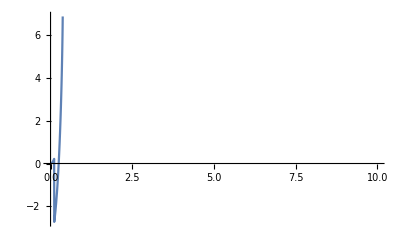

```mathematica
hcom[t_]:=h1[t]/;t<t1
hcom[t_]:=h2[t]/;t1<t<t2
hcom[t_]:=h3[t]/;t2<t<t3
hcom[t_]:=h4[t]/;t3<t<t4

Plot[hcom[t],{t,0,10}]
```

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M0-g,v[0]==0},v[t],t]
v1[t_]=v[t]/.sol1[[1]]

M[t_]=M0-A1*ve*1000*t
sol2=DSolve[{v'[t]==-(ve/M[t])*M'[t]-g,v[0]==vi1},v[t],t]
v2[t_]=v[t]/.sol2[[1]]

sol3=DSolve[{v'[t]==-g-(k*c*(v[t])^(2))/(M2),v[0]==vi2},v[t],t]
v3[t_]=v[t]/.sol3[[1]]

sol4=DSolve[{v'[t]==-g+(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
v4[t_]=v[t]/.sol4[[1]]


h1[t_]=Integrate[v1[t],t]

h2[t_]=Integrate[v2[t],t]

h3[t_]=Integrate[v3[t],t]

h4[t_]=Integrate[v4[t],t]


a1[t_]=D[v1[t],t]

a2[t_]=D[v2[t],t]

a3[t_]=D[v3[t],t]

a4[t_]=D[v4[t],t]


tsol1=Solve[h1[t]==L,t]
vi1=Simplify[v1[t]/.tsol1[[2]]]

M[t_]=M0-A1*ve*1000*t
tsol2=Solve[M[t]==0,t]
vi2=Simplify[v2[t]/.tsol2[[1]]]

tsol3=Solve[v3[t]==0,t]

tsol4=Solve[h4[t]==0,t]





t1=tsol1[[2]]
t1=t/.t1

t2=tsol2[[1]]
t2=t/.t2
t2=t2+t1

t3=tsol3[[1]]
t3=t/.t3
t3=t3+t2

t4=tsol4[[1]]
t4=t/.t4
t4=t4+t3
```

{{v[t]→35.4624 t}}

35.4624 t

0.6889-1.84838 t

{{v[t]→-21.7869-9.81 t-26.0768 Log[0.372705-1. t]}}

-21.7869-9.81 t-26.0768 Log[0.372705-1. t]

{}

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

v[t]/.{}⟦1⟧

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→-(51.8274 (-1.+1. ⅇ^(0.378564 t)))/(1.+1. ⅇ^(0.378564 t))}}

-(51.8274 (-1.+1. ⅇ^(0.378564 t)))/(1.+1. ⅇ^(0.378564 t))

17.7312 t^2

4.28992 t-4.905 t^2+9.71894 Log[0.372705-1. t]-26.0768 t Log[0.372705-1. t]

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

∫(v[t]/.{}⟦1⟧)ⅆt

51.8274 t-273.81 Log[1.+ⅇ^(0.378564 t)]

35.4624

-9.81+26.0768/(0.372705-1. t)

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

∂_t (v[t]/.{}⟦1⟧)

(19.62 ⅇ^(0.378564 t) (-1.+1. ⅇ^(0.378564 t)))/((1.+1. ⅇ^(0.378564 t))^2)-(19.62 ⅇ^(0.378564 t))/(1.+1. ⅇ^(0.378564 t))

{{t→-0.111389},{t→0.111389}}

3.95012

0.6889-1.84838 t

{{t→0.372705}}

Indeterminate

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]]}}

ReplaceAll::reps: {51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Integrate::ilim: Invalid integration variable or limit(s) in 0.484093+(t/.51.8274 Tan[2.30083 (0.682709+Times[«2»])]==0).

ReplaceAll::reps: {51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Integrate::ilim: Invalid integration variable or limit(s) in 0.484093+(System`TSolveDump`X$6648[1]/.51.8274 Tan[2.30083 (0.682709+Times[«2»])]==0).

Integrate::ilim: Invalid integration variable or limit(s) in 23800655/49165411+(System`TSolveDump`X$6648[1]/.(484721255 Tan[(75987449 (80060187/117268331+Times[«2»]))/33026142])/9352607==0).

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[∫(v[0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0)]/.{}⟦1⟧)ⅆ(0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0))-273.81 Log[Cosh[0.189282 t]]+273.81 Log[Sin[0.189282 (0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0))]]==0,t]

{t→0.111389}

0.111389

{t→0.372705}

0.372705

0.484093

{t→v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]]}

v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]]

0.484093+v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]]

∫(v[0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0)]/.{}⟦1⟧)ⅆ(0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0))-273.81 Log[Cosh[0.189282 t]]+273.81 Log[Sin[0.189282 (0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0))]]==0

ReplaceAll::reps: {∫(v[0.484093+ReplaceAll[«2»]]/.{}⟦1⟧)ⅆ(0.484093+(t/.Times[«2»]==0))-273.81 Log[Cosh[0.189282 t]]+273.81 Log[Sin[0.189282 Plus[«2»]]]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

t/.∫(v[0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0)]/.{}⟦1⟧)ⅆ(0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0))-273.81 Log[Cosh[0.189282 t]]+273.81 Log[Sin[0.189282 (0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0))]]==0

0.484093+(t/.∫(v[0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0)]/.{}⟦1⟧)ⅆ(0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0))-273.81 Log[Cosh[0.189282 t]]+273.81 Log[Sin[0.189282 (0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0))]]==0)+v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]]

```mathematica
L=.22
A1=((4.75*10^(-3))^2)*Pi
A2=((.06)^2)*Pi
P1=4.4*10^5
P2=10^5
M0=0.6889
M2=.1889
g=9.81
ve=26.07680962
ρ1=1000
ρ2=1.22
c=0.1
k=ρ2*A2/2
```

0.22

0.0000708822

0.0113097

440000.

100000

0.6889

0.1889

9.81

26.0768

1000

1.22

0.1

0.00689894

```mathematica
t3
```

0.484093+v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]]

```mathematica
t1
```

0.111389

```mathematica
t2
```

0.484093

```mathematica
t3
```

0.484093+v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]]

```mathematica
tsol2
```

{{t→0.372705}}

```mathematica
tsol3
```

{{t→v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]]}}

```mathematica
tsol3=Solve[v3[t]==0,t]
```

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]]}}

```mathematica
v3[t]
```

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

v[t]/.{}⟦1⟧

```mathematica
sol3=DSolve[{v'[t]==-g-(k*c*(v[t])^(2))/(M2),v[0]==vi2},v[t],t]
v3[t_]=v[t]/.sol3[[1]]
```

{}

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

v[t]/.{}⟦1⟧

```mathematica
v2[t_]=v[t]/.sol2[[1]]
```

-21.7869-9.81 t-26.0768 Log[0.372705-1. t]

```mathematica
sol3=DSolve[{v'[t]==-g-(k*c*(v[t])^(2))/(M2),v[0]==vi2},v[t],t]
v3[t_]=v[t]/.sol3[[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→-51.8274 Tan[0.189282 t-1. ArcTan[0.0192948 vi2]]}}

-51.8274 Tan[0.189282 t-1. ArcTan[0.0192948 vi2]]

```mathematica
h3[t_]=Integrate[v3[t],t]
```

(M2 Log[Cos[(√c √g √k t)/(√M2)-ArcTan[(√c √k vi2)/(√g √M2)]]])/(c k)

```mathematica
a3[t_]=D[v3[t],t]
```

-g Sec[(-√c √g √k t+√M2 ArcTan[(√c √k vi2)/(√g √M2)])/(√M2)]^2

```mathematica
tsol3=Solve[v3[t]==0,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→(√M2 ArcTan[(√c √k vi2)/(√g √M2)])/(√c √g √k)}}

```mathematica
h3[t]=h3[t]+h2[t2]
```

h2[t2]+(M2 Log[Cos[(√c √g √k t)/(√M2)-ArcTan[(√c √k vi2)/(√g √M2)]]])/(c k)

```mathematica
t3=tsol3[[1]]
t3=t/.t3
t3=t3+t2
```

{t→(√M2 ArcTan[(√c √k vi2)/(√g √M2)])/(√c √g √k)}

(√M2 ArcTan[(√c √k vi2)/(√g √M2)])/(√c √g √k)

t2+(√M2 ArcTan[(√c √k vi2)/(√g √M2)])/(√c √g √k)

```mathematica
L=.22
A1=((4.75*10^(-3))^2)*Pi
A2=((.06)^2)*Pi
P1=4.4*10^5
P2=10^5
M0=0.6889
M2=.1889
g=9.81
ve=26.07680962
ρ1=1000
ρ2=1.22
c=0.1
k=ρ2*A2/2
```

0.22

0.0000708822

0.0113097

440000.

100000

0.6889

0.1889

9.81

26.0768

1000

1.22

0.1

0.00689894

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M0-g,v[0]==0},v[t],t]
v1[t_]=v[t]/.sol1[[1]]

M[t_]=M0-A1*ve*1000*t
sol2=DSolve[{v'[t]==-(ve/M[t])*M'[t]-g,v[0]==vi1},v[t],t]
v2[t_]=v[t]/.sol2[[1]]

sol3=DSolve[{v'[t]==-g-(k*c*(v[t])^(2))/(M2),v[0]==vi2},v[t],t]
v3[t_]=v[t]/.sol3[[1]]

sol4=DSolve[{v'[t]==-g+(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
v4[t_]=v[t]/.sol4[[1]]


h1[t_]=Integrate[v1[t],t]

h2[t_]=Integrate[v2[t],t]

h3[t_]=Integrate[v3[t],t]

h4[t_]=Integrate[v4[t],t]


a1[t_]=D[v1[t],t]

a2[t_]=D[v2[t],t]

a3[t_]=D[v3[t],t]

a4[t_]=D[v4[t],t]


tsol1=Solve[h1[t]==L,t]
vi1=Simplify[v1[t]/.tsol1[[2]]]

M[t_]=M0-A1*ve*1000*t
tsol2=Solve[M[t]==0,t]
vi2=Simplify[v2[t]/.tsol2[[1]]]

tsol3=Solve[v3[t]==0,t]

tsol4=Solve[h4[t]==0,t]


t1=tsol1[[2]]
t1=t/.t1

t2=tsol2[[1]]
t2=t/.t2
t2=t2+t1

t3=tsol3[[1]]
t3=t/.t3
t3=t3+t2

t4=tsol4[[1]]
t4=t/.t4
t4=t4+t3


h2[t]=h2[t]+h1[t1]

h3[t]=h3[t]+h2[t2]

h4[t]=h4[t]+h3[t3]
```

{{v[t]→(-g M0 t+A1 P1 t)/M0}}

(-g M0 t+A1 P1 t)/M0

M0-1000 A1 t ve

{{v[t]→-g t+vi1+ve Log[M0]-ve Log[M0-1000 A1 t ve]}}

-g t+vi1+ve Log[M0]-ve Log[M0-1000 A1 t ve]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k vi2)/(√g √M2)])/(√M2)])/(√c √k)}}

(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k vi2)/(√g √M2)])/(√M2)])/(√c √k)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→-(√g √M2 Tanh[(√c √g √k t)/(√M2)])/(√c √k)}}

-(√g √M2 Tanh[(√c √g √k t)/(√M2)])/(√c √k)

-(g t^2)/2+(A1 P1 t^2)/(2 M0)

-(g t^2)/2+t ve+t vi1+t ve Log[M0]+(M0 Log[M0-1000 A1 t ve])/(1000 A1)-t ve Log[M0-1000 A1 t ve]

(M2 Log[Cos[(√c √g √k t)/(√M2)-ArcTan[(√c √k vi2)/(√g √M2)]]])/(c k)

-(M2 Log[Cosh[(√c √g √k t)/(√M2)]])/(c k)

(-g M0+A1 P1)/M0

-g+(1000 A1 ve^2)/(M0-1000 A1 t ve)

-g Sec[(-√c √g √k t+√M2 ArcTan[(√c √k vi2)/(√g √M2)])/(√M2)]^2

-g Sech[(√c √g √k t)/(√M2)]^2

{{t→-(√2 √L)/(√(-g+(A1 P1)/M0))},{t→(√2 √L)/(√(-g+(A1 P1)/M0))}}

√2 √L √(-g+(A1 P1)/M0)

M0-1000 A1 t ve

{{t→M0/(1000 A1 ve)}}

√2 √L √(-g+(A1 P1)/M0)-(g M0)/(1000 A1 ve)+ve ∞+ve Log[M0]

Solve::infc: The system (√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[Times[«5»]])/(√M2)])/(√c √k)==0 contains an infinite object ∞.

Solve[(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M0)/(1000 A1 ve)+ve ∞+ve Log[M0]))/(√g √M2)])/(√M2)])/(√c √k)==0,t]

{{t→ConditionalExpression[(2 ⅈ √M2 π C[1])/(√c √g √k),C[1]∈ℤ]}}

{t→(√2 √L)/(√(-g+(A1 P1)/M0))}

(√2 √L)/(√(-g+(A1 P1)/M0))

{t→M0/(1000 A1 ve)}

M0/(1000 A1 ve)

(√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)

(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M0)/(1000 A1 ve)+ve ∞+ve Log[M0]))/(√g √M2)])/(√M2)])/(√c √k)==0

ReplaceAll::reps: {(√g √M2 Tan[(-Power[«2»] Power[«2»] Power[«2»] t+Power[«2»] ArcTan[«1»])/(√M2)])/(√c √k)==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

t/.(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M0)/(1000 A1 ve)+ve ∞+ve Log[M0]))/(√g √M2)])/(√M2)])/(√c √k)==0

(√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)+(t/.(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M0)/(1000 A1 ve)+ve ∞+ve Log[M0]))/(√g √M2)])/(√M2)])/(√c √k)==0)

{t→ConditionalExpression[(2 ⅈ √M2 π C[1])/(√c √g √k),C[1]∈ℤ]}

ConditionalExpression[(2 ⅈ √M2 π C[1])/(√c √g √k),C[1]∈ℤ]

ConditionalExpression[(√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)+(2 ⅈ √M2 π C[1])/(√c √g √k)+(t/.(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M0)/(1000 A1 ve)+ve ∞+ve Log[M0]))/(√g √M2)])/(√M2)])/(√c √k)==0),C[1]∈ℤ]

-(g L)/(-g+(A1 P1)/M0)+(A1 L P1)/(M0 (-g+(A1 P1)/M0))+√2 √L √(-g+(A1 P1)/M0) t-(g t^2)/2+t ve+t ve Log[M0]+(M0 Log[M0-1000 A1 t ve])/(1000 A1)-t ve Log[M0-1000 A1 t ve]

√2 √L √(-g+(A1 P1)/M0) ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve))-1/2 g ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve))^2+((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve+((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve Log[M0]+(M0 Log[M0-1000 A1 ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve])/(1000 A1)-((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve Log[M0-1000 A1 ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve]+(M2 Log[Cos[(√c √g √k t)/(√M2)-ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M0)/(1000 A1 ve)+ve ∞+ve Log[M0]))/(√g √M2)]]])/(c k)

1/(c k)M2 Log[Cos[ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M0)/(1000 A1 ve)+ve ∞+ve Log[M0]))/(√g √M2)]-1/(√M2)√c √g √k ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)+(t/.(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M0)/(1000 A1 ve)+ve ∞+ve Log[M0]))/(√g √M2)])/(√M2)])/(√c √k)==0))]]-(M2 Log[Cosh[(√c √g √k t)/(√M2)]])/(c k)

```mathematica
L=.22
A1=((4.75*10^(-3))^2)*Pi
A2=((.06)^2)*Pi
P1=4.4*10^5
P2=10^5
M0=0.6889
M2=.1889
g=9.81
ve=26.07680962
ρ1=1000
ρ2=1.22
c=0.1
k=ρ2*A2/2
```

0.22

0.0000708822

0.0113097

440000.

100000

0.6889

0.1889

9.81

26.0768

1000

1.22

0.1

0.00689894

```mathematica
hcom[t_]:=h1[t]/;t<t1
hcom[t_]:=h2[t]/;t1<t<t2
hcom[t_]:=h3[t]/;t2<t<t3
hcom[t_]:=h4[t]/;t3<t<t4
```

```mathematica
Plot[hcom[t],{t,0,10}]
```

-Graphics-

```mathematica
tsol1
```

{{t→-0.111389},{t→0.111389}}

```mathematica
t1
```

0.111389

```mathematica
t2
```

0.484093

```mathematica
t3
```

ReplaceAll::reps: {51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0)

```mathematica
t4
```

ReplaceAll::reps: {51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ConditionalExpression[0.484093+(0.+33.1948 ⅈ) C[1]+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0),C[1]∈ℤ]

```mathematica
h3
```

h3

```mathematica
h3[t]
```

(13.2727-9.12529 ⅈ)+273.81 Log[Sin[0.189282 t]]

```mathematica
h02=h1[t1]
h03=h2[t2]
h04=h3[t3]
```

0.22

13.2727-9.12529 ⅈ

ReplaceAll::reps: {51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

273.81 Log[Sin[0.189282 (0.484093+(t/.51.8274 Tan[2.30083 (0.682709-0.082267 t)]==0))]]

```mathematica
h2[t_]=Integrate[v2[t],t]+h02
```

0.22+20.3092 t-4.905 t^2+9.71894 Log[0.6889-1.84838 t]-26.0768 t Log[0.6889-1.84838 t]

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M0-g,v[0]==0},v[t],t]
v1[t_]=v[t]/.sol1[[1]]

M[t_]=M0-A1*ve*1000*t
sol2=DSolve[{v'[t]==-(ve/M[t])*M'[t]-g,v[0]==vi1},v[t],t]
v2[t_]=v[t]/.sol2[[1]]

sol3=DSolve[{v'[t]==-g-(k*c*(v[t])^(2))/(M2),v[0]==vi2},v[t],t]
v3[t_]=v[t]/.sol3[[1]]

sol4=DSolve[{v'[t]==-g+(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
v4[t_]=v[t]/.sol4[[1]]

h02=h1[t1]
h03=h2[t2]
h04=h3[t3]

h1[t_]=Integrate[v1[t],t]

h2[t_]=Integrate[v2[t],t]+h02

h3[t_]=Integrate[v3[t],t]+h03

h4[t_]=Integrate[v4[t],t]+h04


a1[t_]=D[v1[t],t]

a2[t_]=D[v2[t],t]

a3[t_]=D[v3[t],t]

a4[t_]=D[v4[t],t]


tsol1=Solve[h1[t]==L,t]
vi1=Simplify[v1[t]/.tsol1[[2]]]

M[t_]=M0-A1*ve*1000*t
tsol2=Solve[M[t]==0,t]
vi2=Simplify[v2[t]/.tsol2[[1]]]

tsol3=Solve[v3[t]==0,t]

tsol4=Solve[h4[t]==0,t]


t1=tsol1[[2]]
t1=t/.t1

t2=tsol2[[1]]
t2=t/.t2
t2=t2+t1

t3=tsol3[[1]]
t3=t/.t3
t3=t3+t2

t4=tsol4[[1]]
t4=t/.t4
t4=t4+t3
```

{{v[t]→(-g M0 t+A1 P1 t)/M0}}

(-g M0 t+A1 P1 t)/M0

M0-1000 A1 t ve

{{v[t]→√2 √L √((-g M0+A1 P1)/M0)-g t+ve Log[M0]-ve Log[M0-1000 A1 t ve]}}

√2 √L √((-g M0+A1 P1)/M0)-g t+ve Log[M0]-ve Log[M0-1000 A1 t ve]

{}

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

v[t]/.{}⟦1⟧

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→-(√g √M2 Tanh[(√c √g √k t)/(√M2)])/(√c √k)}}

-(√g √M2 Tanh[(√c √g √k t)/(√M2)])/(√c √k)

-(g L)/(-g+(A1 P1)/M0)+(A1 L P1)/(M0 (-g+(A1 P1)/M0))

-(g L)/(-g+(A1 P1)/M0)+(A1 L P1)/(M0 (-g+(A1 P1)/M0))+√2 √L √(-g+(A1 P1)/M0) ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve))-1/2 g ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve))^2+((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve+((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve Log[M0]+(M0 Log[M0-1000 A1 ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve])/(1000 A1)-((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve Log[M0-1000 A1 ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve]

-(g L)/(-g+(A1 P1)/M0)+(A1 L P1)/(M0 (-g+(A1 P1)/M0))+√2 √L √(-g+(A1 P1)/M0) ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve))-1/2 g ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve))^2+((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve+((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve Log[M0]+(M0 Log[M0-1000 A1 ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve])/(1000 A1)-((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve Log[M0-1000 A1 ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve]+1/(c k)M2 Log[Cos[ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M0)/(1000 A1 ve)+ve ∞+ve Log[M0]))/(√g √M2)]-1/(√M2)√c √g √k ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)+(t/.(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M0)/(1000 A1 ve)+ve ∞+ve Log[M0]))/(√g √M2)])/(√M2)])/(√c √k)==0))]]

-(g t^2)/2+(A1 P1 t^2)/(2 M0)

-(g L)/(-g+(A1 P1)/M0)+(A1 L P1)/(M0 (-g+(A1 P1)/M0))+√2 √L √(-g+(A1 P1)/M0) t-(g t^2)/2+t ve+t ve Log[M0]+(M0 Log[M0-1000 A1 t ve])/(1000 A1)-t ve Log[M0-1000 A1 t ve]

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-(g L)/(-g+(A1 P1)/M0)+(A1 L P1)/(M0 (-g+(A1 P1)/M0))+√2 √L √(-g+(A1 P1)/M0) ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve))-1/2 g ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve))^2+((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve+∫(v[t]/.{}⟦1⟧)ⅆt+((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve Log[M0]+(M0 Log[M0-1000 A1 ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve])/(1000 A1)-((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve Log[M0-1000 A1 ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve]

-(g L)/(-g+(A1 P1)/M0)+(A1 L P1)/(M0 (-g+(A1 P1)/M0))+√2 √L √(-g+(A1 P1)/M0) ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve))-1/2 g ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve))^2+((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve+((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve Log[M0]+(M0 Log[M0-1000 A1 ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve])/(1000 A1)-((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve Log[M0-1000 A1 ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve]+1/(c k)M2 Log[Cos[ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M0)/(1000 A1 ve)+ve ∞+ve Log[M0]))/(√g √M2)]-1/(√M2)√c √g √k ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)+(t/.(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M0)/(1000 A1 ve)+ve ∞+ve Log[M0]))/(√g √M2)])/(√M2)])/(√c √k)==0))]]-(M2 Log[Cosh[(√c √g √k t)/(√M2)]])/(c k)

(-g M0+A1 P1)/M0

-g+(1000 A1 ve^2)/(M0-1000 A1 t ve)

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

∂_t (v[t]/.{}⟦1⟧)

-g Sech[(√c √g √k t)/(√M2)]^2

{{t→-(√2 √L)/(√(-g+(A1 P1)/M0))},{t→(√2 √L)/(√(-g+(A1 P1)/M0))}}

√2 √L √(-g+(A1 P1)/M0)

M0-1000 A1 t ve

{{t→M0/(1000 A1 ve)}}

√2 √L √(-g+(A1 P1)/M0)-(g M0)/(1000 A1 ve)+ve ∞+ve Log[M0]

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]]}}

ReplaceAll::reps: {(√g √M2 Tan[(-Power[«2»] Power[«2»] Power[«2»] t+Power[«2»] ArcTan[«1»])/(√M2)])/(√c √k)==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::infc: The system -(g L)/(-g+(A1 P1)/M0)+(A1 L P1)/(M0 (-g+(A1 P1)/M0))+√2 √L √(-g+(A1 P1)/M0) ((√2 √L)/(√(Times[«2»]+Times[«3»]))+M0/(1000 A1 ve))-1/2 g («1»)^2+«1»+«1»+(M0 «1»)/(1000 «2»)-((√2 √L)/(√(Times[«2»]+Times[«3»]))+M0/(1000 A1 ve)) ve Log[M0-1000 A1 (Times[«3»]+Times[«4»]) ve]+(M2 Log[Cos[ArcTan[Times[«5»]]-Power[«2»] Power[«2»] Power[«2»] Power[«2»] Plus[«3»]]])/(c k)-(M2 Log[Cosh[(√c √g √k t)/(√M2)]])/(c k)==0 contains an infinite object ∞.

Solve[-(g L)/(-g+(A1 P1)/M0)+(A1 L P1)/(M0 (-g+(A1 P1)/M0))+√2 √L √(-g+(A1 P1)/M0) ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve))-1/2 g ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve))^2+((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve+((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve Log[M0]+(M0 Log[M0-1000 A1 ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve])/(1000 A1)-((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve Log[M0-1000 A1 ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve]+1/(c k)M2 Log[Cos[ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M0)/(1000 A1 ve)+ve ∞+ve Log[M0]))/(√g √M2)]-1/(√M2)√c √g √k ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)+(t/.(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M0)/(1000 A1 ve)+ve ∞+ve Log[M0]))/(√g √M2)])/(√M2)])/(√c √k)==0))]]-(M2 Log[Cosh[(√c √g √k t)/(√M2)]])/(c k)==0,t]

{t→(√2 √L)/(√(-g+(A1 P1)/M0))}

(√2 √L)/(√(-g+(A1 P1)/M0))

{t→M0/(1000 A1 ve)}

M0/(1000 A1 ve)

(√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)

{t→v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]]}

v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]]

(√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)+v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]]

-(g L)/(-g+(A1 P1)/M0)+(A1 L P1)/(M0 (-g+(A1 P1)/M0))+√2 √L √(-g+(A1 P1)/M0) ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve))-1/2 g ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve))^2+((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve+((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve Log[M0]+(M0 Log[M0-1000 A1 ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve])/(1000 A1)-((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve Log[M0-1000 A1 ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve]+1/(c k)M2 Log[Cos[ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M0)/(1000 A1 ve)+ve ∞+ve Log[M0]))/(√g √M2)]-1/(√M2)√c √g √k ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)+(t/.(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M0)/(1000 A1 ve)+ve ∞+ve Log[M0]))/(√g √M2)])/(√M2)])/(√c √k)==0))]]-(M2 Log[Cosh[(√c √g √k t)/(√M2)]])/(c k)==0

ReplaceAll::reps: {-(g L)/(-g+A1 Power[«2»] P1)+(A1 L P1)/(M0 (-g+A1 Power[«2»] P1))+√2 √L √(-g+A1 Power[«2»] P1) ((√2 √L)/(√Plus[«2»])+M0/(1000 A1 ve))-1/2 g («1»)^2+((«1»)/(√(«1»))+(«2»)/(«1»)) ve+«1»+(M0 Log[M0-«1»])/(1000 A1)-((√2 √L)/(√Plus[«2»])+M0/(1000 A1 ve)) ve Log[M0-1000 A1 Plus[«2»] ve]+(M2 Log[Cos[ArcTan[«1»]+Times[«6»]]])/(c k)-(M2 Log[Cosh[Power[«2»] Power[«2»] Power[«2»] Power[«2»] t]])/(c k)==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

t/.-(g L)/(-g+(A1 P1)/M0)+(A1 L P1)/(M0 (-g+(A1 P1)/M0))+√2 √L √(-g+(A1 P1)/M0) ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve))-1/2 g ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve))^2+((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve+((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve Log[M0]+(M0 Log[M0-1000 A1 ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve])/(1000 A1)-((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve Log[M0-1000 A1 ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve]+1/(c k)M2 Log[Cos[ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M0)/(1000 A1 ve)+ve ∞+ve Log[M0]))/(√g √M2)]-1/(√M2)√c √g √k ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)+(t/.(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M0)/(1000 A1 ve)+ve ∞+ve Log[M0]))/(√g √M2)])/(√M2)])/(√c √k)==0))]]-(M2 Log[Cosh[(√c √g √k t)/(√M2)]])/(c k)==0

(√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)+(t/.-(g L)/(-g+(A1 P1)/M0)+(A1 L P1)/(M0 (-g+(A1 P1)/M0))+√2 √L √(-g+(A1 P1)/M0) ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve))-1/2 g ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve))^2+((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve+((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve Log[M0]+(M0 Log[M0-1000 A1 ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve])/(1000 A1)-((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve Log[M0-1000 A1 ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)) ve]+1/(c k)M2 Log[Cos[ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M0)/(1000 A1 ve)+ve ∞+ve Log[M0]))/(√g √M2)]-1/(√M2)√c √g √k ((√2 √L)/(√(-g+(A1 P1)/M0))+M0/(1000 A1 ve)+(t/.(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M0)/(1000 A1 ve)+ve ∞+ve Log[M0]))/(√g √M2)])/(√M2)])/(√c √k)==0))]]-(M2 Log[Cosh[(√c √g √k t)/(√M2)]])/(c k)==0)+v^(-1)[InverseFunction[ReplaceAll,1,2][0,{}⟦1⟧]]

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M0-g,v[0]==0},v[t],t]
v1[t_]=v[t]/.sol1[[1]]

M[t_]=M0-A1*ve*1000*t
sol2=DSolve[{v'[t]==-(ve/M[t])*M'[t]-g,v[0]==vi1},v[t],t]
v2[t_]=v[t]/.sol2[[1]]

sol3=DSolve[{v'[t]==-g-(k*c*(v[t])^(2))/(M2),v[0]==vi2},v[t],t]
v3[t_]=v[t]/.sol3[[1]]

sol4=DSolve[{v'[t]==-g+(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
v4[t_]=v[t]/.sol4[[1]]

h02=h1[t1]
h03=h2[t2]
h04=h3[t3]

h1[t_]=Integrate[v1[t],t]

h2[t_]=Integrate[v2[t],t]+h02

h3[t_]=Integrate[v3[t],t]+h03

h4[t_]=Integrate[v4[t],t]+h04


a1[t_]=D[v1[t],t]

a2[t_]=D[v2[t],t]

a3[t_]=D[v3[t],t]

a4[t_]=D[v4[t],t]


tsol1=Solve[h1[t]==L,t]
vi1=Simplify[v1[t]/.tsol1[[2]]]

M[t_]=M0-A1*ve*1000*t
tsol2=Solve[M[t]==0,t]
vi2=Simplify[v2[t]/.tsol2[[1]]]

tsol3=Solve[v3[t]==0,t]

tsol4=Solve[h4[t]==0,t]
```

{{v[t]→(-g M0 t+A1 P1 t)/M0}}

(-g M0 t+A1 P1 t)/M0

M0-1000 A1 t ve

{{v[t]→-g t+vi1+ve Log[M0]-ve Log[M0-1000 A1 t ve]}}

-g t+vi1+ve Log[M0]-ve Log[M0-1000 A1 t ve]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k vi2)/(√g √M2)])/(√M2)])/(√c √k)}}

(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k vi2)/(√g √M2)])/(√M2)])/(√c √k)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→-(√g √M2 Tanh[(√c √g √k t)/(√M2)])/(√c √k)}}

-(√g √M2 Tanh[(√c √g √k t)/(√M2)])/(√c √k)

h1[t1]

h2[t2]

h3[t3]

-(g t^2)/2+(A1 P1 t^2)/(2 M0)

-(g t^2)/2-(g t1^2)/2+(A1 P1 t1^2)/(2 M0)+t ve+t vi1+t ve Log[M0]+(M0 Log[M0-1000 A1 t ve])/(1000 A1)-t ve Log[M0-1000 A1 t ve]

-(g t1^2)/2+(A1 P1 t1^2)/(2 M0)-(g t2^2)/2+t2 ve+t2 vi1+t2 ve Log[M0]+(M0 Log[M0-1000 A1 t2 ve])/(1000 A1)-t2 ve Log[M0-1000 A1 t2 ve]+(M2 Log[Cos[(√c √g √k t)/(√M2)-ArcTan[(√c √k vi2)/(√g √M2)]]])/(c k)

-(g t1^2)/2+(A1 P1 t1^2)/(2 M0)-(g t2^2)/2+t2 ve+t2 vi1+t2 ve Log[M0]+(M0 Log[M0-1000 A1 t2 ve])/(1000 A1)-t2 ve Log[M0-1000 A1 t2 ve]+(M2 Log[Cos[(√c √g √k t3)/(√M2)-ArcTan[(√c √k vi2)/(√g √M2)]]])/(c k)-(M2 Log[Cosh[(√c √g √k t)/(√M2)]])/(c k)

(-g M0+A1 P1)/M0

-g+(1000 A1 ve^2)/(M0-1000 A1 t ve)

-g Sec[(-√c √g √k t+√M2 ArcTan[(√c √k vi2)/(√g √M2)])/(√M2)]^2

-g Sech[(√c √g √k t)/(√M2)]^2

{{t→-(√2 √L)/(√(-g+(A1 P1)/M0))},{t→(√2 √L)/(√(-g+(A1 P1)/M0))}}

√2 √L √(-g+(A1 P1)/M0)

M0-1000 A1 t ve

{{t→M0/(1000 A1 ve)}}

√2 √L √(-g+(A1 P1)/M0)-(g M0)/(1000 A1 ve)+ve ∞+ve Log[M0]

Solve::infc: The system (√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[Times[«5»]])/(√M2)])/(√c √k)==0 contains an infinite object ∞.

Solve[(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M0)/(1000 A1 ve)+ve ∞+ve Log[M0]))/(√g √M2)])/(√M2)])/(√c √k)==0,t]

Solve::infc: The system -(g t1^2)/2+(A1 P1 t1^2)/(2 M0)+√2 √L √(-g+(A1 P1)/M0) t2-(g t2^2)/2+t2 ve+t2 ve Log[M0]+(M0 Log[M0-1000 A1 t2 ve])/(1000 A1)-t2 ve Log[M0-1000 A1 t2 ve]+(M2 Log[Cos[Power[«2»] Power[«2»] Power[«2»] Power[«2»] t3-ArcTan[«1»]]])/(c k)-(M2 Log[Cosh[(√c √g √k t)/(√M2)]])/(c k)==0 contains an infinite object ∞.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→-5.28312 ArcCosh[1. ⅇ^(0.0647573 t1^2+0.0741724 t2-0.0179139 t2^2) (0.6889-1.84838 t2)^(0.0354952-0.0952368 t2) Sin[0.189282 t3]]},{t→5.28312 ArcCosh[1. ⅇ^(0.0647573 t1^2+0.0741724 t2-0.0179139 t2^2) (0.6889-1.84838 t2)^(0.0354952-0.0952368 t2) Sin[0.189282 t3]]}}

```mathematica
L=.22
A1=((4.75*10^(-3))^2)*Pi
A2=((.06)^2)*Pi
P1=4.4*10^5
P2=10^5
M0=0.6889
M2=.1889
g=9.81
ve=26.07680962
ρ1=1000
ρ2=1.22
c=0.1
k=ρ2*A2/2
```

0.22

0.0000708822

0.0113097

440000.

100000

0.6889

0.1889

9.81

26.0768

1000

1.22

0.1

0.00689894

```mathematica
t1=tsol1[[2]]
t1=t/.t1

t2=tsol2[[1]]
t2=t/.t2
t2=t2+t1

t3=tsol3[[1]]
t3=t/.t3
t3=t3+t2

t4=tsol4[[1]]
t4=t/.t4
t4=t4+t3
```

{t→0.111389}

0.111389

{t→0.372705}

0.372705

0.484093

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{t→8.2987}

8.2987

8.7828

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{t→-1.68962+0.567203 ⅈ}

-1.68962+0.567203 ⅈ

7.09317+0.567203 ⅈ

```mathematica
tsol4
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→-1.68962+0.567203 ⅈ},{t→1.68962-0.567203 ⅈ}}

```mathematica
h4[t]
```

(12.3416-9.12529 ⅈ)-273.81 Log[Cosh[0.189282 t]]

```mathematica
h03
```

13.4927-9.12529 ⅈ

```mathematica
h3[t]
```

(13.4927-9.12529 ⅈ)+273.81 Log[Sin[0.189282 t]]

```mathematica
h02
```

0.22

```mathematica
h2[t] + .22
```

0.44+20.3092 t-4.905 t^2+9.71894 Log[0.6889-1.84838 t]-26.0768 t Log[0.6889-1.84838 t]

```mathematica
h2[t2]
```

13.4927-9.12529 ⅈ

```mathematica
t2
```

0.484093

```mathematica
t2
```

0.484093

```mathematica
t1
```

0.111389

```mathematica
t2-t1
```

0.372705

```mathematica
h2[t2-t1]
```

Indeterminate

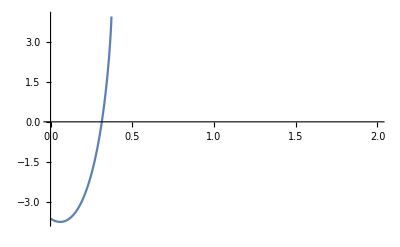

```mathematica
Plot[h2[t],{t,0,2}]
```

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M0-g,v[0]==0},v[t],t]
v1[t_]=v[t]/.sol1[[1]]
```

{{v[t]→(-g M0 t+A1 P1 t)/M0}}

(-g M0 t+A1 P1 t)/M0

```mathematica
M[t_]=M0-A1*ve*1000*t
sol2=DSolve[{v'[t]==-(ve/M[t])*M'[t]-g,v[0]==-vi1},v[t],t]
v2[t_]=v[t]/.sol2[[1]]
```

M0-1000 A1 t ve

```mathematica
{{v[t]->-g t-vi1+ve Log[M0]-ve Log[M0-1000 A1 t ve]}}
```

-g t+vi1+ve Log[M0]-ve Log[M0-1000 A1 t ve]

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M0-g,v[0]==0},v[t],t]
v1[t_]=v[t]/.sol1[[1]]

M[t_]=M0-A1*ve*1000*t
sol2=DSolve[{v'[t]==-(ve/M[t])*M'[t]-g,v[0]==-vi1},v[t],t]
v2[t_]=v[t]/.sol2[[1]]

sol3=DSolve[{v'[t]==-g-(k*c*(v[t])^(2))/(M2),v[0]==vi2},v[t],t]
v3[t_]=v[t]/.sol3[[1]]

sol4=DSolve[{v'[t]==-g+(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
v4[t_]=v[t]/.sol4[[1]]

h02=h1[t1]
h03=h2[t2]
h04=h3[t3]

h1[t_]=Integrate[v1[t],t]

h2[t_]=Integrate[v2[t],t]

h3[t_]=Integrate[v3[t],t]+h03

h4[t_]=Integrate[v4[t],t]+h04


a1[t_]=D[v1[t],t]

a2[t_]=D[v2[t],t]

a3[t_]=D[v3[t],t]

a4[t_]=D[v4[t],t]


tsol1=Solve[h1[t]==L,t]
vi1=Simplify[v1[t]/.tsol1[[2]]]

M[t_]=M0-A1*ve*1000*t
tsol2=Solve[M[t]==0,t]
vi2=Simplify[v2[t]/.tsol2[[1]]]

tsol3=Solve[v3[t]==0,t]

tsol4=Solve[h4[t]==0,t]
```

{{v[t]→(-g M0 t+A1 P1 t)/M0}}

(-g M0 t+A1 P1 t)/M0

M0-1000 A1 t ve

{{v[t]→-g t-vi1+ve Log[M0]-ve Log[M0-1000 A1 t ve]}}

-g t-vi1+ve Log[M0]-ve Log[M0-1000 A1 t ve]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k vi2)/(√g √M2)])/(√M2)])/(√c √k)}}

(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k vi2)/(√g √M2)])/(√M2)])/(√c √k)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→-(√g √M2 Tanh[(√c √g √k t)/(√M2)])/(√c √k)}}

-(√g √M2 Tanh[(√c √g √k t)/(√M2)])/(√c √k)

h1[t1]

h2[t2]

h3[t3]

-(g t^2)/2+(A1 P1 t^2)/(2 M0)

-(g t^2)/2+t ve-t vi1+t ve Log[M0]+(M0 Log[M0-1000 A1 t ve])/(1000 A1)-t ve Log[M0-1000 A1 t ve]

-(g t2^2)/2+t2 ve-t2 vi1+t2 ve Log[M0]+(M0 Log[M0-1000 A1 t2 ve])/(1000 A1)-t2 ve Log[M0-1000 A1 t2 ve]+(M2 Log[Cos[(√c √g √k t)/(√M2)-ArcTan[(√c √k vi2)/(√g √M2)]]])/(c k)

-(g t2^2)/2+t2 ve-t2 vi1+t2 ve Log[M0]+(M0 Log[M0-1000 A1 t2 ve])/(1000 A1)-t2 ve Log[M0-1000 A1 t2 ve]+(M2 Log[Cos[(√c √g √k t3)/(√M2)-ArcTan[(√c √k vi2)/(√g √M2)]]])/(c k)-(M2 Log[Cosh[(√c √g √k t)/(√M2)]])/(c k)

(-g M0+A1 P1)/M0

-g+(1000 A1 ve^2)/(M0-1000 A1 t ve)

-g Sec[(-√c √g √k t+√M2 ArcTan[(√c √k vi2)/(√g √M2)])/(√M2)]^2

-g Sech[(√c √g √k t)/(√M2)]^2

{{t→-(√2 √L)/(√(-g+(A1 P1)/M0))},{t→(√2 √L)/(√(-g+(A1 P1)/M0))}}

√2 √L √(-g+(A1 P1)/M0)

M0-1000 A1 t ve

{{t→M0/(1000 A1 ve)}}

-√2 √L √(-g+(A1 P1)/M0)-(g M0)/(1000 A1 ve)+ve ∞+ve Log[M0]

Solve::infc: The system (√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[Times[«5»]])/(√M2)])/(√c √k)==0 contains an infinite object ∞.

Solve[(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k (-√2 √L √(-g+(A1 P1)/M0)-(g M0)/(1000 A1 ve)+ve ∞+ve Log[M0]))/(√g √M2)])/(√M2)])/(√c √k)==0,t]

Solve::infc: The system -√2 √L √(-g+(A1 P1)/M0) t2-(g t2^2)/2+t2 ve+t2 ve Log[M0]+(M0 Log[M0-1000 A1 t2 ve])/(1000 A1)-t2 ve Log[M0-1000 A1 t2 ve]+(M2 Log[Cos[Power[«2»] Power[«2»] Power[«2»] Power[«2»] t3-ArcTan[«1»]]])/(c k)-(M2 Log[Cosh[(√c √g √k t)/(√M2)]])/(c k)==0 contains an infinite object ∞.

Solve[-√2 √L √(-g+(A1 P1)/M0) t2-(g t2^2)/2+t2 ve+t2 ve Log[M0]+(M0 Log[M0-1000 A1 t2 ve])/(1000 A1)-t2 ve Log[M0-1000 A1 t2 ve]+(M2 Log[Cos[(√c √g √k t3)/(√M2)-ArcTan[(√c √k (-√2 √L √(-g+(A1 P1)/M0)-(g M0)/(1000 A1 ve)+ve ∞+ve Log[M0]))/(√g √M2)]]])/(c k)-(M2 Log[Cosh[(√c √g √k t)/(√M2)]])/(c k)==0,t]

0.22

0.0000708822

0.0113097

440000.

100000

0.6889

0.1889

9.81

26.0768

1000

1.22

0.1

0.00689894

{t→0.111389}

0.111389

{t→0.372705}

0.372705

0.484093

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{t→8.2987}

8.2987

8.7828

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{t→-1.45392+0.652759 ⅈ}

-1.45392+0.652759 ⅈ

7.32887+0.652759 ⅈ

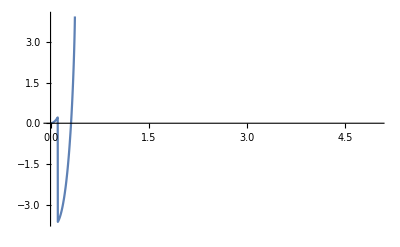

```mathematica
L=.22
A1=((4.75*10^(-3))^2)*Pi
A2=((.06)^2)*Pi
P1=4.4*10^5
P2=10^5
M0=0.6889
M2=.1889
g=9.81
ve=26.07680962
ρ1=1000
ρ2=1.22
c=0.1
k=ρ2*A2/2

t1=tsol1[[2]]
t1=t/.t1

t2=tsol2[[1]]
t2=t/.t2
t2=t2+t1

t3=tsol3[[1]]
t3=t/.t3
t3=t3+t2

t4=tsol4[[1]]
t4=t/.t4
t4=t4+t3

hcom[t_]:=h1[t]/;t<t1
hcom[t_]:=h2[t]/;t1<t<t2
hcom[t_]:=h3[t]/;t2<t<t3
hcom[t_]:=h4[t]/;t3<t<t4

Plot[hcom[t],{t,0,5}]
```

```mathematica
h2[t]
```

12.4089 t-4.905 t^2+9.71894 Log[0.6889-1.84838 t]-26.0768 t Log[0.6889-1.84838 t]

```mathematica
tsol3
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→8.2987}}

```mathematica
tsol4
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→-1.45392+0.652759 ⅈ},{t→1.45392-0.652759 ⅈ}}

```mathematica
h3[t]
```

(9.4482-9.12529 ⅈ)+273.81 Log[Sin[0.189282 t]]

```mathematica
h2[t]
```

12.4089 t-4.905 t^2+9.71894 Log[0.6889-1.84838 t]-26.0768 t Log[0.6889-1.84838 t]

```mathematica
h2[t2]
```

9.4482-9.12529 ⅈ

```mathematica
tsol2=M1/M'[t]
```

-0.541014 M1

```mathematica
M1=.5
```

0.5

```mathematica
tsol2=M1/(A1*ve*1000)
```

0.270507

```mathematica
t2=tsol2[[1]]
t2=t/.t2
t2=t2+t1
```

Part::partd: Part specification 0.270507⟦1⟧ is longer than depth of object.

0.270507⟦1⟧

ReplaceAll::reps: {0.270507⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

t/.0.270507⟦1⟧

0.111389+(t/.0.270507⟦1⟧)

```mathematica
M[t_]=M0-A1*ve*1000*t
t2=M1/(A1*ve*1000)
vi2=Simplify[v2[t]/.t2[[1]]]
```

0.6889-1.84838 t

0.270507

Part::partd: Part specification 0.270507⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {0.270507⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-29.6871-9.81 t-26.0768 Log[0.372705-1. t]/.0.270507⟦1⟧

```mathematica
M[t_]=M0-A1*ve*1000*t
t2=M1/(A1*ve*1000)
vi2=Simplify[v2[t]/.t2]
```

0.6889-1.84838 t

0.270507

ReplaceAll::reps: {0.270507} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-29.6871-9.81 t-26.0768 Log[0.372705-1. t]/.0.270507

```mathematica
M[t_]=M0-A1*ve*1000*t
t2=M1/(A1*ve*1000)
vi2=v2[t2]
```

0.6889-1.84838 t

0.270507

27.1364

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M0-g,v[0]==0},v[t],t]
v1[t_]=v[t]/.sol1[[1]]

M[t_]=M0-A1*ve*1000*t
sol2=DSolve[{v'[t]==-(ve/M[t])*M'[t]-g,v[0]==vi1},v[t],t]
v2[t_]=v[t]/.sol2[[1]]

sol3=DSolve[{v'[t]==-g-(k*c*(v[t])^(2))/(M2),v[0]==vi2},v[t],t]
v3[t_]=v[t]/.sol3[[1]]

sol4=DSolve[{v'[t]==-g+(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
v4[t_]=v[t]/.sol4[[1]]

h02=h1[t1]
h03=h2[t2]
h04=h3[t3]

h1[t_]=Integrate[v1[t],t]

h2[t_]=Integrate[v2[t],t]+h02

h3[t_]=Integrate[v3[t],t]+h03

h4[t_]=Integrate[v4[t],t]+h04


a1[t_]=D[v1[t],t]

a2[t_]=D[v2[t],t]

a3[t_]=D[v3[t],t]

a4[t_]=D[v4[t],t]


tsol1=Solve[h1[t]==L,t]
vi1=Simplify[v1[t]/.tsol1[[2]]]

M[t_]=M0-A1*ve*1000*t
t2=M1/(A1*ve*1000)
vi2=v2[t2]

tsol3=Solve[v3[t]==0,t]

tsol4=Solve[h4[t]==0,t]
```

{{v[t]→(-g M0 t+A1 P1 t)/M0}}

(-g M0 t+A1 P1 t)/M0

M0-1000 A1 t ve

{{v[t]→-g t+vi1+ve Log[M0]-ve Log[M0-1000 A1 t ve]}}

-g t+vi1+ve Log[M0]-ve Log[M0-1000 A1 t ve]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k vi2)/(√g √M2)])/(√M2)])/(√c √k)}}

(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k vi2)/(√g √M2)])/(√M2)])/(√c √k)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→-(√g √M2 Tanh[(√c √g √k t)/(√M2)])/(√c √k)}}

-(√g √M2 Tanh[(√c √g √k t)/(√M2)])/(√c √k)

h1[t1]

h2[t2]

h3[t3]

-(g t^2)/2+(A1 P1 t^2)/(2 M0)

-(g t^2)/2-(g t1^2)/2+(A1 P1 t1^2)/(2 M0)+t ve+t vi1+t ve Log[M0]+(M0 Log[M0-1000 A1 t ve])/(1000 A1)-t ve Log[M0-1000 A1 t ve]

-(g t1^2)/2+(A1 P1 t1^2)/(2 M0)-(g t2^2)/2+t2 ve+t2 vi1+t2 ve Log[M0]+(M0 Log[M0-1000 A1 t2 ve])/(1000 A1)-t2 ve Log[M0-1000 A1 t2 ve]+(M2 Log[Cos[(√c √g √k t)/(√M2)-ArcTan[(√c √k vi2)/(√g √M2)]]])/(c k)

-(g t1^2)/2+(A1 P1 t1^2)/(2 M0)-(g t2^2)/2+t2 ve+t2 vi1+t2 ve Log[M0]+(M0 Log[M0-1000 A1 t2 ve])/(1000 A1)-t2 ve Log[M0-1000 A1 t2 ve]+(M2 Log[Cos[(√c √g √k t3)/(√M2)-ArcTan[(√c √k vi2)/(√g √M2)]]])/(c k)-(M2 Log[Cosh[(√c √g √k t)/(√M2)]])/(c k)

(-g M0+A1 P1)/M0

-g+(1000 A1 ve^2)/(M0-1000 A1 t ve)

-g Sec[(-√c √g √k t+√M2 ArcTan[(√c √k vi2)/(√g √M2)])/(√M2)]^2

-g Sech[(√c √g √k t)/(√M2)]^2

{{t→-(√2 √L)/(√(-g+(A1 P1)/M0))},{t→(√2 √L)/(√(-g+(A1 P1)/M0))}}

√2 √L √(-g+(A1 P1)/M0)

M0-1000 A1 t ve

M1/(1000 A1 ve)

√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→(√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)])/(√c √g √k)}}

{{t→ConditionalExpression[1/(√c √g √k)√M2 (-ArcCosh[ⅇ^(((2000 c k M1)/A1-1000000 c g k t1^2+(1000000 A1 c k P1 t1^2)/M0-(c g k M1^2)/(A1^2 ve^2)+(2000 √2 c k √L M1 √((-g M0+A1 P1)/M0))/(A1 ve)+(2000 c k M1 Log[M0])/A1+(2000 c k M0 Log[M0-M1])/A1-(2000 c k M1 Log[M0-M1])/A1+2000000 M2 Log[Cos[(√c √g √k t3)/(√M2)-ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)]]])/(2000000 M2))]+2 ⅈ π C[1]),-π<1/2000000 Im[1/M2((2000 c k M1)/A1-1000000 c g k t1^2+(1000000 A1 c k P1 t1^2)/M0-(c g k M1^2)/(A1^2 ve^2)+(2000 √2 c k √L M1 √((-g M0+A1 P1)/M0))/(A1 ve)+(2000 c k M1 Log[M0])/A1+(2000 c k M0 Log[M0-M1])/A1-(2000 c k M1 Log[M0-M1])/A1+2000000 M2 Log[Cos[(√c √g √k t3)/(√M2)-ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)]]])]≤π&&C[1]∈ℤ]},{t→ConditionalExpression[1/(√c √g √k)√M2 (ArcCosh[ⅇ^(((2000 c k M1)/A1-1000000 c g k t1^2+(1000000 A1 c k P1 t1^2)/M0-(c g k M1^2)/(A1^2 ve^2)+(2000 √2 c k √L M1 √((-g M0+A1 P1)/M0))/(A1 ve)+(2000 c k M1 Log[M0])/A1+(2000 c k M0 Log[M0-M1])/A1-(2000 c k M1 Log[M0-M1])/A1+2000000 M2 Log[Cos[(√c √g √k t3)/(√M2)-ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)]]])/(2000000 M2))]+2 ⅈ π C[1]),-π<1/2000000 Im[1/M2((2000 c k M1)/A1-1000000 c g k t1^2+(1000000 A1 c k P1 t1^2)/M0-(c g k M1^2)/(A1^2 ve^2)+(2000 √2 c k √L M1 √((-g M0+A1 P1)/M0))/(A1 ve)+(2000 c k M1 Log[M0])/A1+(2000 c k M0 Log[M0-M1])/A1-(2000 c k M1 Log[M0-M1])/A1+2000000 M2 Log[Cos[(√c √g √k t3)/(√M2)-ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)]]])]≤π&&C[1]∈ℤ]}}

```mathematica
L=.22
A1=((4.75*10^(-3))^2)*Pi
A2=((.06)^2)*Pi
P1=4.4*10^5
P2=10^5
M0=0.6889
M1=.5
M2=.1889
g=9.81
ve=26.07680962
ρ1=1000
ρ2=1.22
c=0.1
k=ρ2*A2/2
```

0.22

0.0000708822

0.0113097

440000.

100000

0.6889

0.5

0.1889

9.81

26.0768

1000

1.22

0.1

0.00689894

```mathematica
t1=tsol1[[2]]
t1=t/.t1

t3=tsol3[[1]]
t3=t/.t3
t3=t3+t2

t4=tsol4[[1]]
t4=t/.t4
t4=t4+t3
```

{t→0.111389}

0.111389

{t→3.14057}

3.14057

3.41108

{t→ConditionalExpression[5.28312 (-0.0636619+2 ⅈ π C[1]),C[1]∈ℤ]}

ConditionalExpression[5.28312 (-0.0636619+2 ⅈ π C[1]),C[1]∈ℤ]

ConditionalExpression[3.41108+5.28312 (-0.0636619+2 ⅈ π C[1]),C[1]∈ℤ]

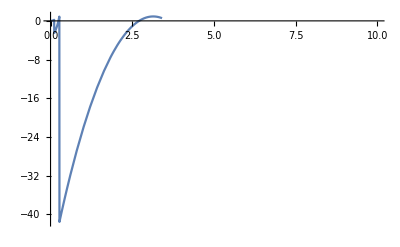

```mathematica
hcom[t_]:=h1[t]/;t<t1
hcom[t_]:=h2[t]/;t1<t<t2
hcom[t_]:=h3[t]/;t2<t<t3
hcom[t_]:=h4[t]/;t3<t<t4

Plot[hcom[t],{t,0,10}]
```

```mathematica
h04
```

0.554479

```mathematica
h02
```

0.22

```mathematica
h03
```

0.913555

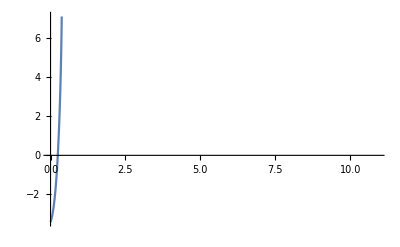

```mathematica
Plot[h2[t],{t,0,10.91}]
```

```mathematica
Plot[h1[t],{t,0,10.91}]
```

-Graphics-

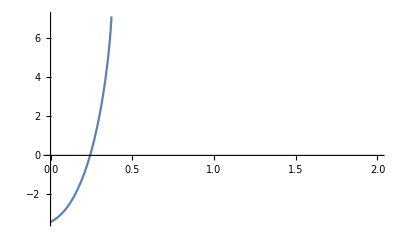

```mathematica
Plot[h2[t],{t,0,2}]
```

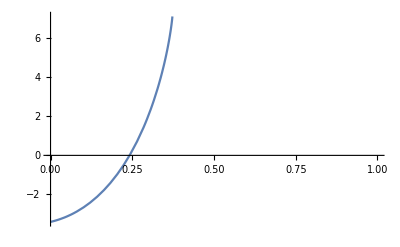

```mathematica
Plot[h2[t],{t,0,1}]
```

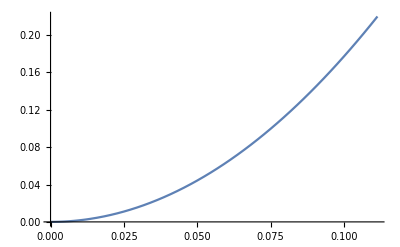

```mathematica
Plot[h1[t],{t,0,t1}]
```

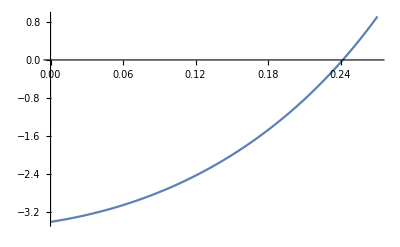

```mathematica
Plot[h2[t],{t,0,t2}]
```

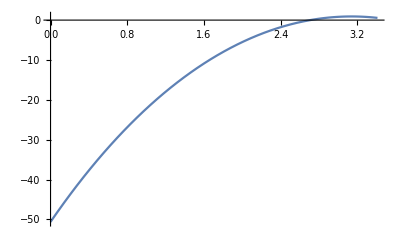

```mathematica
Plot[h3[t],{t,0,t3}]
```

```mathematica
Plot[h4[t]-h4[0],{t,0,5}]
```

-Graphics-

```mathematica
hcom[t_]:=h1[t]/;t<t1
hcom[t_]:=h2[t]/;t1<t<t2
hcom[t_]:=h3[t]/;t2<t<t3
hcom[t_]:=h4[t]/;t3<t<5
```

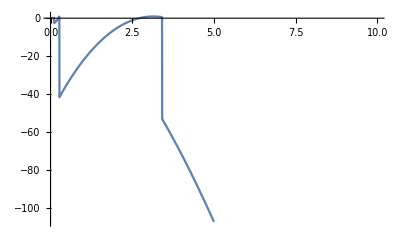

```mathematica
Plot[hcom[t],{t,0,10}]
```

```mathematica
h1[t_]=h1[t]
h2[t_]=h2[t] + h02
h3[t_]=h3[t] + h03
h4[t_]=h4[t] + h04
```

17.7312 t^2

10.88+20.3092 t-4.905 t^2+9.71894 Log[0.6889-1.84838 t]-26.0768 t Log[0.6889-1.84838 t]

12.4871+273.81 Log[Cos[0.594454-0.189282 t]]

0.554479-273.81 Log[Cosh[0.189282 t]]

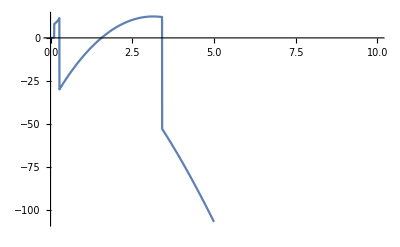

```mathematica
hcom[t_]:=h1[t]/;t<t1
hcom[t_]:=h2[t]/;t1<t<t2
hcom[t_]:=h3[t]/;t2<t<t3
hcom[t_]:=h4[t]/;t3<t<5

Plot[hcom[t],{t,0,10}]
```

```mathematica
h1[t]=h1[t_]
h2[t]=h2[t_]+5
h3[t]=h3[t_]
h4[t]=h4[t_]
```

17.7312 t_^2

15.88+9.71894 Log[0.6889-1.84838 t_]+20.3092 t_-26.0768 Log[0.6889-1.84838 t_] t_-4.905 t_^2

12.4871+273.81 Log[Cos[0.594454-0.189282 t_]]

0.554479-273.81 Log[Cosh[0.189282 t_]]

```mathematica
h1[t]=h1[t]
h2[t]=h2[t]+h02
h3[t]=h3[t]
h4[t]=h4[t]
```

17.7312 t_^2

21.32+9.71894 Log[0.6889-1.84838 t_]+20.3092 t_-26.0768 Log[0.6889-1.84838 t_] t_-4.905 t_^2

12.4871+273.81 Log[Cos[0.594454-0.189282 t_]]

0.554479-273.81 Log[Cosh[0.189282 t_]]

```mathematica
clear [h2[t]]
```

clear[21.32+9.71894 Log[0.6889-1.84838 t_]+20.3092 t_-26.0768 Log[0.6889-1.84838 t_] t_-4.905 t_^2]

{{v[t]→(-g M0 t+A1 P1 t)/M0}}

(-g M0 t+A1 P1 t)/M0

M0-1000 A1 t ve

{{v[t]→-g t+vi1+ve Log[M0]-ve Log[M0-1000 A1 t ve]}}

-g t+vi1+ve Log[M0]-ve Log[M0-1000 A1 t ve]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k vi2)/(√g √M2)])/(√M2)])/(√c √k)}}

(√g √M2 Tan[(-√c √g √k t+√M2 ArcTan[(√c √k vi2)/(√g √M2)])/(√M2)])/(√c √k)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→-(√g √M2 Tanh[(√c √g √k t)/(√M2)])/(√c √k)}}

-(√g √M2 Tanh[(√c √g √k t)/(√M2)])/(√c √k)

h1[t1]

h2[t2]

h3[t3]

-(g t^2)/2+(A1 P1 t^2)/(2 M0)

-(g t^2)/2+t ve+t vi1+t ve Log[M0]+(M0 Log[M0-1000 A1 t ve])/(1000 A1)-t ve Log[M0-1000 A1 t ve]

(M2 Log[Cos[(√c √g √k t)/(√M2)-ArcTan[(√c √k vi2)/(√g √M2)]]])/(c k)

-(M2 Log[Cosh[(√c √g √k t)/(√M2)]])/(c k)

-(g t^2)/2+(A1 P1 t^2)/(2 M0)

5-(g t^2)/2+t ve+t vi1+t ve Log[M0]+(M0 Log[M0-1000 A1 t ve])/(1000 A1)-t ve Log[M0-1000 A1 t ve]

(M2 Log[Cos[(√c √g √k t)/(√M2)-ArcTan[(√c √k vi2)/(√g √M2)]]])/(c k)

-(M2 Log[Cosh[(√c √g √k t)/(√M2)]])/(c k)

(-g M0+A1 P1)/M0

-g+(1000 A1 ve^2)/(M0-1000 A1 t ve)

-g Sec[(-√c √g √k t+√M2 ArcTan[(√c √k vi2)/(√g √M2)])/(√M2)]^2

-g Sech[(√c √g √k t)/(√M2)]^2

{{t→-(√2 √L)/(√(-g+(A1 P1)/M0))},{t→(√2 √L)/(√(-g+(A1 P1)/M0))}}

√2 √L √(-g+(A1 P1)/M0)

M0-1000 A1 t ve

M1/(1000 A1 ve)

√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→(√M2 ArcTan[(√c √k (√2 √L √(-g+(A1 P1)/M0)-(g M1)/(1000 A1 ve)+ve Log[M0]-ve Log[M0-M1]))/(√g √M2)])/(√c √g √k)}}

{{t→ConditionalExpression[(2 ⅈ √M2 π C[1])/(√c √g √k),C[1]∈ℤ]}}

0.22

0.0000708822

0.0113097

440000.

100000

0.6889

0.5

0.1889

9.81

26.0768

1000

1.22

0.1

0.00689894

{t→0.111389}

0.111389

{t→3.14057}

3.14057

3.41108

{t→ConditionalExpression[(0.+33.1948 ⅈ) C[1],C[1]∈ℤ]}

ConditionalExpression[(0.+33.1948 ⅈ) C[1],C[1]∈ℤ]

ConditionalExpression[3.41108+(0.+33.1948 ⅈ) C[1],C[1]∈ℤ]

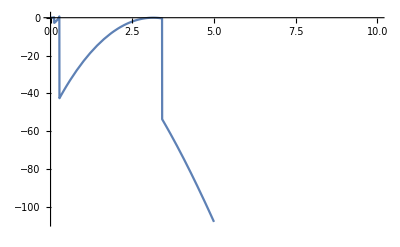

```mathematica
sol1=DSolve[{v'[t]==(P1*A1)/M0-g,v[0]==0},v[t],t]
v1[t_]=v[t]/.sol1[[1]]

M[t_]=M0-A1*ve*1000*t
sol2=DSolve[{v'[t]==-(ve/M[t])*M'[t]-g,v[0]==vi1},v[t],t]
v2[t_]=v[t]/.sol2[[1]]

sol3=DSolve[{v'[t]==-g-(k*c*(v[t])^(2))/(M2),v[0]==vi2},v[t],t]
v3[t_]=v[t]/.sol3[[1]]

sol4=DSolve[{v'[t]==-g+(k*c*(v[t])^2)/(M2),v[0]==0},v[t],t]
v4[t_]=v[t]/.sol4[[1]]

h02=h1[t1]
h03=h2[t2]
h04=h3[t3]

h1[t_]=Integrate[v1[t],t]

h2[t_]=Integrate[v2[t],t]

h3[t_]=Integrate[v3[t],t]

h4[t_]=Integrate[v4[t],t]

h1[t]=h1[t]
h2[t]=h2[t]+h02
h3[t]=h3[t] + h03
h4[t]=h4[t] + h04

a1[t_]=D[v1[t],t]

a2[t_]=D[v2[t],t]

a3[t_]=D[v3[t],t]

a4[t_]=D[v4[t],t]


tsol1=Solve[h1[t]==L,t]
vi1=Simplify[v1[t]/.tsol1[[2]]]

M[t_]=M0-A1*ve*1000*t
t2=M1/(A1*ve*1000)
vi2=v2[t2]

tsol3=Solve[v3[t]==0,t]

tsol4=Solve[h4[t]==0,t]

L=.22
A1=((4.75*10^(-3))^2)*Pi
A2=((.06)^2)*Pi
P1=4.4*10^5
P2=10^5
M0=0.6889
M1=.5
M2=.1889
g=9.81
ve=26.07680962
ρ1=1000
ρ2=1.22
c=0.1
k=ρ2*A2/2

t1=tsol1[[2]]
t1=t/.t1

t3=tsol3[[1]]
t3=t/.t3
t3=t3+t2

t4=tsol4[[1]]
t4=t/.t4
t4=t4+t3

hcom[t_]:=h1[t]/;t<t1
hcom[t_]:=h2[t]/;t1<t<t2
hcom[t_]:=h3[t]/;t2<t<t3
hcom[t_]:=h4[t]/;t3<t<5

Plot[hcom[t],{t,0,10}]
```